## Initialization

### Load images

```mathematica
validationRoot="/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated";
validationImages="images";
validationResult="molfiles";
validationDumps="dumps";
```

```mathematica
<<"/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Drafts/ChemicalLines.wl"
```

```mathematica
SetDirectory["/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Outputs"];
```

```mathematica
images=Import[FileNameJoin[{validationRoot,validationDumps,"images.mx"}]];
```

### Save the images

```mathematica
imFilePaths=FileNames[All,FileNameJoin[{validationRoot,validationImages}]];
```

```mathematica
images=Import[#]&/@imFilePaths;
```

```mathematica
Export[FileNameJoin[{validationRoot,validationDumps,"images.mx"}],images]
```

/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated/dumps/images.mx

## One image

Tested on 10, then 1493

```mathematica
i=images[[1493]]
```

-Graphics-

```mathematica
i=Rasterize@Graphics[{White,EdgeForm[Black],RegularPolygon[6]}]
```

-Graphics-

## Line Detect

### Future

```mathematica
i2=ColorNegate@Dilation[ColorNegate@i,1]
```

-Graphics-

```mathematica
visualizeLongLineDetect[i2,{0.05,0.03},{0.03,0.02,0.01},30]
```

| t = 0.05 | t = 0.03
d=0.03 | -Graphics- | -Graphics-
d=0.02 | -Graphics- | -Graphics-
d=0.01 | -Graphics- | -Graphics-

```mathematica
visualizeLongLineDetect[i2,{0.01,0.09},{0.01},30]
```

| t = 0.01 | t = 0.09
d=0.01 | -Graphics- | -Graphics-

```mathematica
allLinesN=doLongLineDetect[i2,0.05,0.01,25];
showLines[i2,allLinesN]
```

-Graphics-

### Current

```mathematica
allLines=doLineDetect[i,0.05,0.01];
showLines[i,allLines]
```

-Graphics-

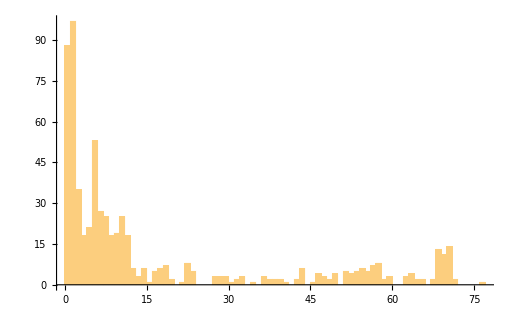

```mathematica
Histogram[lineDistance/@Flatten[flattenLines/@allLines],{1}]
```

```mathematica
showLines[i,Complement[Flatten[flattenLines/@allLines],longLines]]
```

-Graphics-

## Long Lines

```mathematica
lineSize=30;
```

```mathematica
longLines=pickLongLines[allLines,lineSize];
showLines[i,longLines]
```

-Graphics-

## Parallel Lines

### Newest

```mathematica
degreeTolerance=10;
parallelLongLinesByAngle=Gather[Sort[longLines],Not[degreeTolerance<Abs[lineAngle[#1]/Degree-lineAngle[#2]/Degree]<(180-degreeTolerance)]&];
```

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,parallelLongLinesByAngle[[n]]],ImageSize->Medium],{n,1,Length[parallelLongLinesByAngle],1}]
```

### Old

```mathematica
parallelLongLines=gatherParallelLines[longLines,0.5];
showLines[i,parallelLongLines]
```

-Graphics-

### Future

#### Group by distance, then angle?

```mathematica
nearbyLines=gatherNearbyLinesByCenter[longLines,200];
```

```mathematica
Manipulate[HighlightImage[i,nearbyLines[[n]],ImageSize->Small],{n,1,Length[nearbyLines],1}]
```

```mathematica
degreeTolerance=10;
parallelNearbyLinesByAngle=Gather[#,Not[degreeTolerance<Abs[lineAngle[#1]/Degree-lineAngle[#2]/Degree]<(180-degreeTolerance)]&]&/@nearbyLines;
```

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,parallelNearbyLinesByAngle[[n]]],ImageSize->Medium],{n,1,Length[parallelNearbyLinesByAngle],1}]
```

#### Fix rule for gathering!

```mathematica
gatheredAngles=Gather[longLines,Abs[Mod[lineAngle[#1]/Degree,180]-Mod[lineAngle[#2]/Degree,180]]<15&];
```

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,gatheredAngles[[n]]]],{n,1,Length[gatheredAngles],1}]
```

### Tests

#### Compare line angle mod 180

```mathematica
lineAngle/@longLines
```

{-0.522164,-0.522164,-0.522164,-0.522164,-0.522164,-0.522164,-1.55502,-1.55502,-0.823413,0.783246,-0.840627,0.788984,-1.55502,-1.24803,-0.516426,-0.608235,1.56075,-1.32262,1.55502,-0.464784,0.774639,-1.2882,-0.863579,-0.26682,0.62258,1.53493,0.215178,1.2509,0.218047,-0.788984,1.27959,-0.263951,0.539378,0.539378,0.547986,-1.54354,0.539378,-0.243868,0.510688,-1.35132,-0.588152,-1.34845,0.513557,-0.906615,-0.674223,-1.49764,-0.464784,0.0344284,-1.52059,0.464784,1.06441,-0.461915,-0.545117,-0.591021,-0.0401665,0.4447,0.854972,-1.23368,1.53206,0.464784,0.98121,0.697175,0.481998,1.32549,0.840627,0.461915,-0.588152,-0.450438,-0.456176,0.840627,1.52059,-0.312725,0.585283,-0.588152,0.722997,0.556593,0.717259,-0.200832,-0.332808,0.281165,-0.611104,0.576676,-0.329939,1.20786,1.1304,0.605366,0.152059,-0.542247,-0.197963,-0.456176,0.605366,1.18491,-0.430355,0.286903,0.441831,0.613973,1.34845}

```mathematica
Manipulate[{1/Degree*lineAngle[Line[{{x,y},{c,d}}]],Graphics[{Gray,Disk[{0,0},10],Red,Line[{{x,y},{c,d}}]}],lineToPointDelta[Line[{{x,y},{c,d}}]]},{{x,0},-10,10},{{y,0},-10,10},{c,-10,10},{d,-10,10}]
```

```mathematica
(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&[{{a,b},{c,d}}]//TraditionalForm
```

(d-b)/(c-a)

```mathematica
CoordinateTransform["Cartesian"->"Polar",First@Line[{{a,b},{c,d}}]]
```

{{√(a^2+b^2),ArcTan[a,b]},{√(c^2+d^2),ArcTan[c,d]}}

```mathematica
First@Line[{{a,b},{c,d}}]
```

{{a,b},{c,d}}

```mathematica
Map[lineSlope,parallelLongLines]
```

{{{-0.575439},{-0.575439},{-0.575439},{-0.575439},{-0.575439},{-0.575439},{-0.567826},{-0.696295},{-0.501421},{-0.273338},{-1.0072},{-0.270257},{-0.24882},{-0.666883},{-0.799151},{-0.501421},{-0.497836},{-0.606406},{-0.671035},{-0.666883},{-0.483596},{-0.490696},{-0.323334},{-0.666883},{-0.203577},{-0.345665},{-0.700564},{-0.342457},{-0.602489},{-0.200591},{-0.490696},{-0.459051}},{{-63.3673},{-63.3673},{-63.3673}},{{-1.07907},{-1.11704},{-1.17},{-1.27742}},{{0.995706},{1.0072},{0.97871},{0.717812},{0.598585},{0.598585},{0.610337},{0.598585},{0.560262},{0.564038},{0.501421},{1.14981},{0.501421},{1.49486},{0.837471},{0.523153},{1.11704},{0.497836},{1.11704},{0.662745},{0.882384},{0.622213},{0.872229},{0.650428},{0.692044},{0.692044},{0.70485}},{{-2.98987},{-3.44387},{-2.85315}},{{99.5822}},{{-3.94641},{-4.42305}},{{63.3673}},{{27.872}},{{0.218561},{0.221569},{0.034442},{-0.0401881},{0.476535},{0.288816},{0.153242},{0.295044},{0.47302}},{{3.01864},{3.33636},{2.63328}},{{-36.6803}},{{-4.4828}},{{-13.6442}},{{-19.9004}},{{1.80303},{2.12195}},{{25.8056}},{{3.9945},{4.42305}},{{19.9004}},{{2.46152}}}

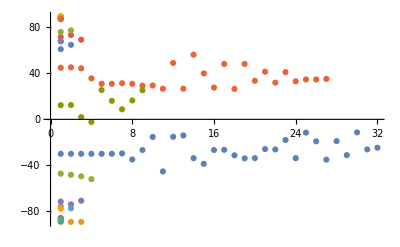

```mathematica
angles=Map[lineAngle,parallelLongLines,{2}]/Degree;
ListPlot@angles
```

Try gathering by line angle

```mathematica
gatheredAngles=Gather[longLines,Abs[lineAngle[#1]-lineAngle[#2]]<1*Degree&];
```

```mathematica
HighlightImage[i,Map[{RandomColor[],#}&,gatheredAngles[[1;;9]]]]
```

-Graphics-

1 degree is too strict

```mathematica
gatheredAngles=Gather[longLines,Abs[(lineAngle[#1]-lineAngle[#2])/Degree]<1&];
```

```mathematica
HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,gatheredAngles[[9]]]]
```

-Graphics-

```mathematica
gatheredAngles=Gather[longLines,Mod[(lineAngle[#1]-lineAngle[#2])/Degree,180]<9&];
```

```mathematica
Gather[longLines,Mod[(lineAngle[#1]-lineAngle[#2])/Degree,180]<9&]
```

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,gatheredAngles[[n]]]],{n,1,Length[gatheredAngles],1}]
```

Part::partd: Part specification gatheredAngles⟦3⟧ is longer than depth of object.

Part::pkspec1: The expression {RGBColor[0.5677477972977687, 0.8921212829687262, 0.7110869610825243],3} cannot be used as a part specification.

Part::partd: Part specification gatheredAngles⟦3⟧ is longer than depth of object.

Part::pkspec1: The expression {RGBColor[0.46557998582232596, 0.7623689114000609, 0.9434951591431735],3} cannot be used as a part specification.

Problem with lines being grouped into parallel while being far away. I will group by distance first.

```mathematica
HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,gatheredAngles[[{1,9}]]]]
```

-Graphics-

#### Try group by distance, then by angle

```mathematica
nearbyLines=gatherNearbyLinesByCenter[longLines,60];
```

```mathematica
Manipulate[HighlightImage[i,nearbyLines[[n]]],{n,1,Length[nearbyLines],1}]
```

```mathematica
parallelNearbyLinesByAngle=Gather[#,Mod[(lineAngle[#1]-lineAngle[#2])/Degree,180]<50&]&/@nearbyLines;
```

```mathematica
showLines[i,parallelNearbyLinesByAngle[[1,5]]]
```

-Graphics-

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],#}&,parallelNearbyLinesByAngle[[n]]]],{n,1,Length[nearbyLines],1}]
```

Part::partd: Part specification parallelNearbyLinesByAngle⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression {RGBColor[0.2409021962307667, 0.7773749996288992, 0.4131700686073889],1} cannot be used as a part specification.

Part::partd: Part specification parallelNearbyLinesByAngle⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression {RGBColor[0.8763197189434544, 0.19851895131299258, 0.5634481644791804],1} cannot be used as a part specification.

#### Make a histogram of the angles of the lines

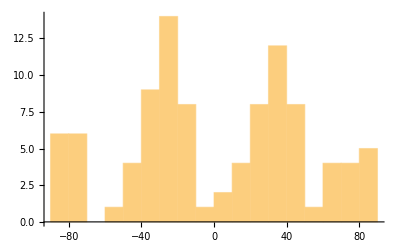

```mathematica
angles=Map[lineAngle,longLines,{1}]/Degree;
Histogram[angles,{10}]
```

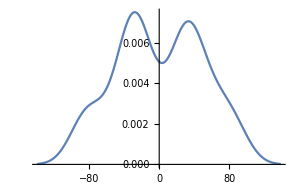

```mathematica
SmoothHistogram[angles]
```

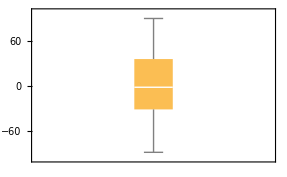

```mathematica
BoxWhiskerChart[angles]
```

I can take the local max of the histogram and round the adjacent ones to that, then group by that.

#### Fun with allLines

```mathematica
Flatten@flattenLines@allLines
```

{Line[{{120.044,603.65},{179.849,569.236}}],813,Line[{{56.999,574.517},{56.8097,562.519}}]}
 |  |  |  |

```mathematica
gatheredAngles=Gather[Flatten@flattenLines@allLines,Mod[lineAngle[#1]-lineAngle[#2],180]<1*Degree&];
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

Gather::smtst: Application of the SameTest function yielded (Mod[lineAngle[#1]-lineAngle[#2],180]<1 °&)[Line[{{120.044,603.65},{179.849,569.236}}],Line[{{129.352,664.147},{129.352,664.147}}]], which evaluates to Indeterminate<°. The SameTest function must evaluate to True or False at every pair of elements.

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

Gather::smtst: Application of the SameTest function yielded (Mod[lineAngle[#1]-lineAngle[#2],180]<1 °&)[Line[{{129.352,664.147},{129.352,664.147}}],Line[{{66.9471,700.057},{63.9135,701.803}}]], which evaluates to Indeterminate<°. The SameTest function must evaluate to True or False at every pair of elements.

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

Gather::smtst: Application of the SameTest function yielded (Mod[lineAngle[#1]-lineAngle[#2],180]<1 °&)[Line[{{129.352,664.147},{129.352,664.147}}],Line[{{408.732,571.518},{409.82,502.526}}]], which evaluates to Indeterminate<°. The SameTest function must evaluate to True or False at every pair of elements.

General::stop: Further output of Gather::smtst will be suppressed during this calculation.

```mathematica
gatheredAngles[[1]]
```

{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{292.959,504.148},{354.064,468.985}}],Line[{{294.9,568.884},{235.095,603.298}}],Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{401.943,507.288},{400.643,508.036}}],Line[{{302.701,564.395},{301.834,564.894}}],Line[{{409.743,569.808},{351.238,603.474}}],Line[{{236.828,669.31},{177.023,703.724}}]}

```mathematica
HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,gatheredAngles[[13]]]]
```

-Graphics-

#### Figuring out gathering parallel lines

Old:

```mathematica
parallelNearbyLinesByAngle=Gather[#,Abs[Mod[lineAngle[#1]/Degree,180]-Mod[lineAngle[#2]/Degree,180]]<10&]&/@nearbyLines;
```

```mathematica
Mod[-88,180]
```

92

```mathematica
Mod[-1,180]
```

179

```mathematica
Mod[-1,360]
```

359

```mathematica
Mod[1,360]
```

1

```mathematica
Mod[-89,90]
```

1

```mathematica
testSetsOfAngles={{1,2},{40,42},{89.5,-89.5},{1,-1},{45,-45}}
```

{{1,2},{40,42},{89.5,-89.5},{1,-1},{45,-45}}

```mathematica
Mod[#[[1]],180]-Mod[#[[2]],180]&/@testSetsOfAngles
```

{-1,-2,-1.,-178,-90}

```mathematica
Mod[#[[1]],180]-Mod[#[[2]],180]&/@testSetsOfAngles
```

{-1,-2,-1.,-178,-90}

```mathematica
Mod[#[[1]],180]-Mod[#[[2]],180]&/@testSetsOfAngles
```

```mathematica
Abs[#[[1]]-#[[2]]]&/@testSetsOfAngles
```

{1,2,179.,2,90}

```mathematica
Mod[Abs[#[[1]]-#[[2]]],90]&/@testSetsOfAngles
```

{1,2,89.,2}

```mathematica
Not[2<Abs[#[[1]]-#[[2]]]<178]&/@testSetsOfAngles
```

{True,True,True,True,False}

```mathematica
Mod[179,90]
```

89

```mathematica
Abs[Mod[#[[1]],90]-Mod[#[[2]],90]]&/@testSetsOfAngles
```

{1,2,89.,88}

## Nearby Lines

### Newest

```mathematica
nearbyParallelLinesByAngle=Map[gatherNearbyLinesByCenter[#,80]&,parallelLongLinesByAngle];
```

```mathematica
Manipulate[HighlightImage[i,nearbyParallelLinesByAngle[[n,m]],ImageSize->Medium],{{m,1,"Close Set"},1,10,1},{{n,1,"Parallel Set"},1,Length@nearbyParallelLinesByAngle,1}]
```

```mathematica
showLines[i,nearbyParallelLinesByAngle[[1,1]]]
```

-Graphics-

### Current

```mathematica
nearbyParallelLines=Map[gatherNearbyLinesByCenter[#,100]&,parallelLongLines];
```

```mathematica
HighlightImage[i,Map[{RandomColor[],Tooltip[#,#]}&,nearbyParallelLines,{2}]]
```

-Graphics-

### Future

### Tests

#### Mapping line colors for HighlightImage

```mathematica
{RandomColor[],#}&/@{a,b,c}
```

{{RGBColor[0.9487319206129217, 0.8734460138761027, 0.7214317099927869],a},{RGBColor[0.17634186768537607, 0.3929663602701017, 0.659159543757067],b},{RGBColor[0.7880751613511954, 0.7939775543382255, 0.9674319528555173],c}}

```mathematica
Map[{RandomColor[],#}&,{a,b,c}]
```

{{RGBColor[0.4992482181854958, 0.06756690486552408, 0.19693544555342468],a},{RGBColor[0.8352980898827223, 0.20570129709994212, 0.6724952549746552],b},{RGBColor[0.758776959933898, 0.3726646792313084, 0.1614252859650276],c}}

```mathematica
Map[{RandomColor[],#}&,{{a},{b},{c}},{2}]
```

{{{RGBColor[0.8265624312570157, 0.9374680524589234, 0.6729222065295466],a}},{{RGBColor[0.9032608668942104, 0.6600966761286842, 0.7630485408782091],b}},{{RGBColor[0.04265310275768841, 0.1572834416542912, 0.2536734366519764],c}}}

## Intersecting Lines

### Newest

```mathematica
intersectingNearbyParallelLinesByAngle=Map[gatherIntersectingLines,nearbyParallelLinesByAngle,{2}];
```

```mathematica
showLines[i,intersectingNearbyParallelLinesByAngle[[1,1]]]
```

-Graphics-

### Current

#### Gather intersecting lines

```mathematica
intersectingNearbyParallelLines=Map[gatherIntersectingLines,nearbyParallelLines,{2}];
```

```mathematica
HighlightImage[i,Map[{RandomColor[],#}&,intersectingNearbyParallelLines,{2}]]
```

-Graphics-

#### Merge the ones that are intersecting

```mathematica
flatIntersectingNearbyParallelLines=Map[Union@*Flatten,intersectingNearbyParallelLines,{3}]
```

{{{{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{135.175,602.152},{177.697,580.983}}]}},{{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]}},{{Line[{{276.1,578.186},{240.809,601.867}}],Line[{{294.9,568.884},{235.095,603.298}}]}},{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}},{{Line[{{392.069,581.316},{359.301,597.394}}],Line[{{409.691,567.931},{367.676,595.95}}],Line[{{409.743,569.808},{351.238,603.474}}]}},{{Line[{{216.895,679.014},{188.639,698.809}}],Line[{{236.828,669.31},{177.023,703.724}}]}},{{Line[{{308.704,286.034},{359.14,257.395}}],Line[{{315.09,281.19},{346.599,265.952}}],Line[{{316.564,293.024},{358.994,264.728}}],Line[{{412.001,299.489},{439.839,282.717}}]}},{{Line[{{408.277,303.162},{465.723,263.162}}],Line[{{435.124,285.81},{464.028,262.711}}]}},{{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]}},{{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{181.465,126.948},{215.962,115.023}}],Line[{{189.121,122.316},{233.706,113.239}}]}},{{Line[{{439.649,202.118},{479.81,161.669}}]}},{{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{271.1,41.235},{308.848,33.6631}}],Line[{{277.669,41.9128},{312.201,30.0873}}]}},{{Line[{{276.567,159.431},{344.011,142.65}}],Line[{{287.353,150.036},{330.646,136.037}}]}}},{{{Line[{{408.732,571.518},{409.82,502.526}}]}},{{Line[{{412.171,353.545},{413.031,299.052}}]}},{{Line[{{235.898,671.505},{237.011,601.014}}]}}},{{{Line[{{588.956,124.609},{551.572,164.95}}]}},{{Line[{{551.019,239.366},{531.91,263.776}}],Line[{{573.949,227.168},{528.593,277.832}}]}},{{Line[{{443.025,201.883},{487.206,150.191}}]}}},{{{Line[{{249.122,49.9212},{227.778,26.0792}}],Line[{{343.168,73.904},{313.82,41.1213}}],Line[{{350.933,78.2382},{325.31,55.8893}}],Line[{{360.89,78.3026},{312.349,29.9702}}]}},{{Line[{{267.194,149.811},{245.866,125.288}}],Line[{{272.719,152.113},{244.975,127.633}}],Line[{{278.159,159.78},{230.248,111.525}}]}},{{Line[{{249.911,48.9246},{201.313,1.36146}}]}},{{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{375.285,279.829},{413.917,303.866}}],Line[{{401.619,298.92},{372.103,274.2}}]}},{{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{248.399,475.992},{294.733,503.727}}]}},{{Line[{{350.933,468.511},{409.708,503.693}}],Line[{{351.366,479.99},{395.679,502.051}}],Line[{{361.809,473.143},{390.59,493.06}}]}},{{Line[{{292.403,569.319},{345.568,597.132}}],Line[{{293.203,567.697},{352.954,604.165}}],Line[{{324.494,584.948},{351.467,603.96}}]}},{{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{135.429,669.9},{177.443,690.966}}],Line[{{140.201,679.024},{170.215,699.795}}]}},{{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{190.289,574.942},{225.497,597.842}}]}},{{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{82.522,579.151},{115.447,600.973}}]}},{{Line[{{368.02,182.964},{347.17,151.795}}]}}},{{{Line[{{355.154,265.002},{371.966,214.739}}]}},{{Line[{{230.405,113.831},{249.785,47.0879}}]}},{{Line[{{341.657,144.053},{351.91,114.798}}]}}},{{{Line[{{352.157,471.012},{351.605,416.015}}]}}},{{{Line[{{343.381,144.53},{360.452,77.159}}]}},{{Line[{{242.699,106.849},{254.387,55.1542}}]}}},{{{Line[{{294.298,571.018},{293.193,501.027}}]}}},{{{Line[{{228.772,664.532},{226.944,613.565}}]}}},{{{Line[{{487.492,150.103},{553.924,164.622}}],Line[{{502.944,160.952},{534.648,170.109}}]}},{{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{468.053,262.983},{498.745,272.038}}],Line[{{474.461,266.822},{509.552,272.199}}]}},{{Line[{{392.683,202.009},{444.641,199.921}}],Line[{{392.767,200.04},{444.736,201.83}}]}},{{Line[{{85.3089,583.804},{124.127,602.302}}]}},{{Line[{{197.065,581.699},{227.8,596.238}}]}}},{{{Line[{{464.496,265.047},{442.64,199.073}}]}},{{Line[{{569.01,210.074},{551.259,163.331}}],Line[{{573.636,230.022},{553.395,162.491}}]}}},{{{Line[{{120.073,671.516},{121.995,601.042}}]}}},{{{Line[{{355.455,269.939},{361.986,240.659}}]}}},{{{Line[{{350.715,471.653},{353.09,439.24}}]}}},{{{Line[{{300.942,556.2},{303.074,513.754}}]}}},{{{Line[{{359.29,172.703},{345.862,144.208}}],Line[{{366.296,183.739},{342.773,141.326}}]}}},{{{Line[{{122.085,656.044},{119.936,600.586}}]}}},{{{Line[{{465.981,250.339},{454.689,205.231}}]}},{{Line[{{562.997,199.406},{556.051,168.682}}]}}},{{{Line[{{413.994,353.456},{411.937,312.508}}]}}},{{{Line[{{461.039,250.841},{446.925,216.098}}]}}}}

```mathematica
mergedIntersectingNearbyParallelLines=Map[mergeLines,flatIntersectingNearbyParallelLines,{1}]
```

{mergeLines[{{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]},{Line[{{276.1,578.186},{240.809,601.867}}],Line[{{294.9,568.884},{235.095,603.298}}]},{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{392.069,581.316},{359.301,597.394}}],Line[{{409.691,567.931},{367.676,595.95}}],Line[{{409.743,569.808},{351.238,603.474}}]},{Line[{{216.895,679.014},{188.639,698.809}}],Line[{{236.828,669.31},{177.023,703.724}}]},{Line[{{308.704,286.034},{359.14,257.395}}],Line[{{315.09,281.19},{346.599,265.952}}],Line[{{316.564,293.024},{358.994,264.728}}],Line[{{412.001,299.489},{439.839,282.717}}]},{Line[{{408.277,303.162},{465.723,263.162}}],Line[{{435.124,285.81},{464.028,262.711}}]},{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]},{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{181.465,126.948},{215.962,115.023}}],Line[{{189.121,122.316},{233.706,113.239}}]},{Line[{{439.649,202.118},{479.81,161.669}}]},{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{271.1,41.235},{308.848,33.6631}}],Line[{{277.669,41.9128},{312.201,30.0873}}]},{Line[{{276.567,159.431},{344.011,142.65}}],Line[{{287.353,150.036},{330.646,136.037}}]}}],mergeLines[{{Line[{{408.732,571.518},{409.82,502.526}}]},{Line[{{412.171,353.545},{413.031,299.052}}]},{Line[{{235.898,671.505},{237.011,601.014}}]}}],mergeLines[{{Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{551.019,239.366},{531.91,263.776}}],Line[{{573.949,227.168},{528.593,277.832}}]},{Line[{{443.025,201.883},{487.206,150.191}}]}}],mergeLines[{{Line[{{249.122,49.9212},{227.778,26.0792}}],Line[{{343.168,73.904},{313.82,41.1213}}],Line[{{350.933,78.2382},{325.31,55.8893}}],Line[{{360.89,78.3026},{312.349,29.9702}}]},{Line[{{267.194,149.811},{245.866,125.288}}],Line[{{272.719,152.113},{244.975,127.633}}],Line[{{278.159,159.78},{230.248,111.525}}]},{Line[{{249.911,48.9246},{201.313,1.36146}}]},{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{375.285,279.829},{413.917,303.866}}],Line[{{401.619,298.92},{372.103,274.2}}]},{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{248.399,475.992},{294.733,503.727}}]},{Line[{{350.933,468.511},{409.708,503.693}}],Line[{{351.366,479.99},{395.679,502.051}}],Line[{{361.809,473.143},{390.59,493.06}}]},{Line[{{292.403,569.319},{345.568,597.132}}],Line[{{293.203,567.697},{352.954,604.165}}],Line[{{324.494,584.948},{351.467,603.96}}]},{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{135.429,669.9},{177.443,690.966}}],Line[{{140.201,679.024},{170.215,699.795}}]},{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{190.289,574.942},{225.497,597.842}}]},{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{82.522,579.151},{115.447,600.973}}]},{Line[{{368.02,182.964},{347.17,151.795}}]}}],mergeLines[{{Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{230.405,113.831},{249.785,47.0879}}]},{Line[{{341.657,144.053},{351.91,114.798}}]}}],mergeLines[{{Line[{{352.157,471.012},{351.605,416.015}}]}}],mergeLines[{{Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{242.699,106.849},{254.387,55.1542}}]}}],mergeLines[{{Line[{{294.298,571.018},{293.193,501.027}}]}}],mergeLines[{{Line[{{228.772,664.532},{226.944,613.565}}]}}],mergeLines[{{Line[{{487.492,150.103},{553.924,164.622}}],Line[{{502.944,160.952},{534.648,170.109}}]},{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{468.053,262.983},{498.745,272.038}}],Line[{{474.461,266.822},{509.552,272.199}}]},{Line[{{392.683,202.009},{444.641,199.921}}],Line[{{392.767,200.04},{444.736,201.83}}]},{Line[{{85.3089,583.804},{124.127,602.302}}]},{Line[{{197.065,581.699},{227.8,596.238}}]}}],mergeLines[{{Line[{{464.496,265.047},{442.64,199.073}}]},{Line[{{569.01,210.074},{551.259,163.331}}],Line[{{573.636,230.022},{553.395,162.491}}]}}],mergeLines[{{Line[{{120.073,671.516},{121.995,601.042}}]}}],mergeLines[{{Line[{{355.455,269.939},{361.986,240.659}}]}}],mergeLines[{{Line[{{350.715,471.653},{353.09,439.24}}]}}],mergeLines[{{Line[{{300.942,556.2},{303.074,513.754}}]}}],mergeLines[{{Line[{{359.29,172.703},{345.862,144.208}}],Line[{{366.296,183.739},{342.773,141.326}}]}}],mergeLines[{{Line[{{122.085,656.044},{119.936,600.586}}]}}],mergeLines[{{Line[{{465.981,250.339},{454.689,205.231}}]},{Line[{{562.997,199.406},{556.051,168.682}}]}}],mergeLines[{{Line[{{413.994,353.456},{411.937,312.508}}]}}],mergeLines[{{Line[{{461.039,250.841},{446.925,216.098}}]}}]}

```mathematica
merged=Map[mergeLines,intersectingNearbyParallelLines,{4}];
```

```mathematica
showLines[i,mergedIntersectingNearbyParallelLines[[1]]]
```

-Graphics-

```mathematica
showLines[i,merged[[1,2]]]
```

-Graphics-

### Future

Merge the parallel groups that contain no overlapping lines.

### Tests

#### Get the single lines.

```mathematica
singles=Cases[intersectingNearbyParallelLines,{_Line},{4}]
```

{{Line[{{120.044,603.65},{179.849,569.236}}]},{Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{316.564,293.024},{358.994,264.728}}]},{Line[{{412.001,299.489},{439.839,282.717}}]},{Line[{{439.649,202.118},{479.81,161.669}}]},{Line[{{276.567,159.431},{344.011,142.65}}]},{Line[{{287.353,150.036},{330.646,136.037}}]},{Line[{{408.732,571.518},{409.82,502.526}}]},{Line[{{412.171,353.545},{413.031,299.052}}]},{Line[{{235.898,671.505},{237.011,601.014}}]},{Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{551.019,239.366},{531.91,263.776}}]},{Line[{{573.949,227.168},{528.593,277.832}}]},{Line[{{443.025,201.883},{487.206,150.191}}]},{Line[{{249.122,49.9212},{227.778,26.0792}}]},{Line[{{360.89,78.3026},{312.349,29.9702}}]},{Line[{{249.911,48.9246},{201.313,1.36146}}]},{Line[{{351.366,479.99},{395.679,502.051}}]},{Line[{{135.429,669.9},{177.443,690.966}}]},{Line[{{368.02,182.964},{347.17,151.795}}]},{Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{230.405,113.831},{249.785,47.0879}}]},{Line[{{341.657,144.053},{351.91,114.798}}]},{Line[{{352.157,471.012},{351.605,416.015}}]},{Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{242.699,106.849},{254.387,55.1542}}]},{Line[{{294.298,571.018},{293.193,501.027}}]},{Line[{{228.772,664.532},{226.944,613.565}}]},{Line[{{487.492,150.103},{553.924,164.622}}]},{Line[{{502.944,160.952},{534.648,170.109}}]},{Line[{{85.3089,583.804},{124.127,602.302}}]},{Line[{{197.065,581.699},{227.8,596.238}}]},{Line[{{464.496,265.047},{442.64,199.073}}]},{Line[{{120.073,671.516},{121.995,601.042}}]},{Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{350.715,471.653},{353.09,439.24}}]},{Line[{{300.942,556.2},{303.074,513.754}}]},{Line[{{122.085,656.044},{119.936,600.586}}]},{Line[{{465.981,250.339},{454.689,205.231}}]},{Line[{{562.997,199.406},{556.051,168.682}}]},{Line[{{413.994,353.456},{411.937,312.508}}]},{Line[{{461.039,250.841},{446.925,216.098}}]}}

#### Get the sets of lines to be merged.

```mathematica
m=Cases[intersectingNearbyParallelLines,{{Repeated[_Line,{2}]}..},{3}]
```

{{{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{322.29,485.05},{354.609,469.192}}]},{Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]}},{{Line[{{294.9,568.884},{235.095,603.298}}],Line[{{276.1,578.186},{240.809,601.867}}]}},{{Line[{{409.743,569.808},{351.238,603.474}}],Line[{{409.691,567.931},{367.676,595.95}}]},{Line[{{409.743,569.808},{351.238,603.474}}],Line[{{392.069,581.316},{359.301,597.394}}]},{Line[{{409.691,567.931},{367.676,595.95}}],Line[{{392.069,581.316},{359.301,597.394}}]}},{{Line[{{236.828,669.31},{177.023,703.724}}],Line[{{216.895,679.014},{188.639,698.809}}]}},{{Line[{{408.277,303.162},{465.723,263.162}}],Line[{{435.124,285.81},{464.028,262.711}}]}},{{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]}},{{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{189.121,122.316},{233.706,113.239}}]},{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{181.465,126.948},{215.962,115.023}}]},{Line[{{189.121,122.316},{233.706,113.239}}],Line[{{181.465,126.948},{215.962,115.023}}]}},{{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{277.669,41.9128},{312.201,30.0873}}]},{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{271.1,41.235},{308.848,33.6631}}]},{Line[{{277.669,41.9128},{312.201,30.0873}}],Line[{{271.1,41.235},{308.848,33.6631}}]}},{{Line[{{278.159,159.78},{230.248,111.525}}],Line[{{267.194,149.811},{245.866,125.288}}]},{Line[{{278.159,159.78},{230.248,111.525}}],Line[{{272.719,152.113},{244.975,127.633}}]},{Line[{{267.194,149.811},{245.866,125.288}}],Line[{{272.719,152.113},{244.975,127.633}}]}},{{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{401.619,298.92},{372.103,274.2}}]},{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{375.285,279.829},{413.917,303.866}}]},{Line[{{401.619,298.92},{372.103,274.2}}],Line[{{375.285,279.829},{413.917,303.866}}]}},{{Line[{{248.399,475.992},{294.733,503.727}}],Line[{{247.168,477.244},{296.781,502.12}}]}},{{Line[{{293.203,567.697},{352.954,604.165}}],Line[{{292.403,569.319},{345.568,597.132}}]},{Line[{{293.203,567.697},{352.954,604.165}}],Line[{{324.494,584.948},{351.467,603.96}}]},{Line[{{292.403,569.319},{345.568,597.132}}],Line[{{324.494,584.948},{351.467,603.96}}]}},{{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{190.289,574.942},{225.497,597.842}}]}},{{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{82.522,579.151},{115.447,600.973}}]}},{{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{474.461,266.822},{509.552,272.199}}]},{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{468.053,262.983},{498.745,272.038}}]},{Line[{{474.461,266.822},{509.552,272.199}}],Line[{{468.053,262.983},{498.745,272.038}}]}},{{Line[{{392.767,200.04},{444.736,201.83}}],Line[{{392.683,202.009},{444.641,199.921}}]}},{{Line[{{573.636,230.022},{553.395,162.491}}],Line[{{569.01,210.074},{551.259,163.331}}]}},{{Line[{{366.296,183.739},{342.773,141.326}}],Line[{{359.29,172.703},{345.862,144.208}}]}}}

```mathematica
mergeLines[Union[Flatten[m[[1]]]]]
```

Line[{{292.959,504.148},{354.609,469.192}}]

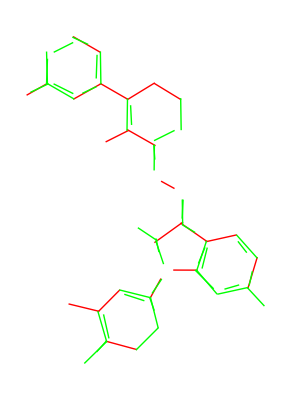

```mathematica
Graphics[{Red,Map[mergeLines,m,{1}],Green,singles}]
```

#### Conflicting level problems

```mathematica
Flatten[intersectingNearbyParallelLines,{3}]
```

{{{{{Line[{{120.044,603.65},{179.849,569.236}}]},{Line[{{135.175,602.152},{177.697,580.983}}]}},{{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{322.29,485.05},{354.609,469.192}}]},{Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]}},{{Line[{{294.9,568.884},{235.095,603.298}}],Line[{{276.1,578.186},{240.809,601.867}}]}},{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]},{Line[{{209.505,686.895},{175.424,702.54}}]}},{{Line[{{409.743,569.808},{351.238,603.474}}],Line[{{409.691,567.931},{367.676,595.95}}]},{Line[{{409.743,569.808},{351.238,603.474}}],Line[{{392.069,581.316},{359.301,597.394}}]},{Line[{{409.691,567.931},{367.676,595.95}}],Line[{{392.069,581.316},{359.301,597.394}}]}},{{Line[{{236.828,669.31},{177.023,703.724}}],Line[{{216.895,679.014},{188.639,698.809}}]}},{{Line[{{308.704,286.034},{359.14,257.395}}],Line[{{315.09,281.19},{346.599,265.952}}]},{Line[{{316.564,293.024},{358.994,264.728}}]},{Line[{{412.001,299.489},{439.839,282.717}}]}},{{Line[{{408.277,303.162},{465.723,263.162}}],Line[{{435.124,285.81},{464.028,262.711}}]}},{{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]}},{{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{189.121,122.316},{233.706,113.239}}]},{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{181.465,126.948},{215.962,115.023}}]},{Line[{{189.121,122.316},{233.706,113.239}}],Line[{{181.465,126.948},{215.962,115.023}}]}},{{Line[{{439.649,202.118},{479.81,161.669}}]}},{{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{277.669,41.9128},{312.201,30.0873}}]},{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{271.1,41.235},{308.848,33.6631}}]},{Line[{{277.669,41.9128},{312.201,30.0873}}],Line[{{271.1,41.235},{308.848,33.6631}}]}},{{Line[{{276.567,159.431},{344.011,142.65}}]},{Line[{{287.353,150.036},{330.646,136.037}}]}}},{{{Line[{{408.732,571.518},{409.82,502.526}}]}},{{Line[{{412.171,353.545},{413.031,299.052}}]}},{{Line[{{235.898,671.505},{237.011,601.014}}]}}},{{{Line[{{588.956,124.609},{551.572,164.95}}]}},{{Line[{{551.019,239.366},{531.91,263.776}}]},{Line[{{573.949,227.168},{528.593,277.832}}]}},{{Line[{{443.025,201.883},{487.206,150.191}}]}}},{{{Line[{{343.168,73.904},{313.82,41.1213}}],Line[{{350.933,78.2382},{325.31,55.8893}}]},{Line[{{249.122,49.9212},{227.778,26.0792}}]},{Line[{{360.89,78.3026},{312.349,29.9702}}]}},{{Line[{{278.159,159.78},{230.248,111.525}}],Line[{{267.194,149.811},{245.866,125.288}}]},{Line[{{278.159,159.78},{230.248,111.525}}],Line[{{272.719,152.113},{244.975,127.633}}]},{Line[{{267.194,149.811},{245.866,125.288}}],Line[{{272.719,152.113},{244.975,127.633}}]}},{{Line[{{249.911,48.9246},{201.313,1.36146}}]}},{{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{401.619,298.92},{372.103,274.2}}]},{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{375.285,279.829},{413.917,303.866}}]},{Line[{{401.619,298.92},{372.103,274.2}}],Line[{{375.285,279.829},{413.917,303.866}}]}},{{Line[{{248.399,475.992},{294.733,503.727}}],Line[{{247.168,477.244},{296.781,502.12}}]}},{{Line[{{350.933,468.511},{409.708,503.693}}],Line[{{361.809,473.143},{390.59,493.06}}]},{Line[{{351.366,479.99},{395.679,502.051}}]}},{{Line[{{293.203,567.697},{352.954,604.165}}],Line[{{292.403,569.319},{345.568,597.132}}]},{Line[{{293.203,567.697},{352.954,604.165}}],Line[{{324.494,584.948},{351.467,603.96}}]},{Line[{{292.403,569.319},{345.568,597.132}}],Line[{{324.494,584.948},{351.467,603.96}}]}},{{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{140.201,679.024},{170.215,699.795}}]},{Line[{{135.429,669.9},{177.443,690.966}}]}},{{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{190.289,574.942},{225.497,597.842}}]}},{{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{82.522,579.151},{115.447,600.973}}]}},{{Line[{{368.02,182.964},{347.17,151.795}}]}}},{{{Line[{{355.154,265.002},{371.966,214.739}}]}},{{Line[{{230.405,113.831},{249.785,47.0879}}]}},{{Line[{{341.657,144.053},{351.91,114.798}}]}}},{{{Line[{{352.157,471.012},{351.605,416.015}}]}}},{{{Line[{{343.381,144.53},{360.452,77.159}}]}},{{Line[{{242.699,106.849},{254.387,55.1542}}]}}},{{{Line[{{294.298,571.018},{293.193,501.027}}]}}},{{{Line[{{228.772,664.532},{226.944,613.565}}]}}},{{{Line[{{487.492,150.103},{553.924,164.622}}]},{Line[{{502.944,160.952},{534.648,170.109}}]}},{{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{474.461,266.822},{509.552,272.199}}]},{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{468.053,262.983},{498.745,272.038}}]},{Line[{{474.461,266.822},{509.552,272.199}}],Line[{{468.053,262.983},{498.745,272.038}}]}},{{Line[{{392.767,200.04},{444.736,201.83}}],Line[{{392.683,202.009},{444.641,199.921}}]}},{{Line[{{85.3089,583.804},{124.127,602.302}}]}},{{Line[{{197.065,581.699},{227.8,596.238}}]}}},{{{Line[{{464.496,265.047},{442.64,199.073}}]}},{{Line[{{573.636,230.022},{553.395,162.491}}],Line[{{569.01,210.074},{551.259,163.331}}]}}},{{{Line[{{120.073,671.516},{121.995,601.042}}]}}},{{{Line[{{355.455,269.939},{361.986,240.659}}]}}},{{{Line[{{350.715,471.653},{353.09,439.24}}]}}},{{{Line[{{300.942,556.2},{303.074,513.754}}]}}},{{{Line[{{366.296,183.739},{342.773,141.326}}],Line[{{359.29,172.703},{345.862,144.208}}]}}},{{{Line[{{122.085,656.044},{119.936,600.586}}]}}},{{{Line[{{465.981,250.339},{454.689,205.231}}]}},{{Line[{{562.997,199.406},{556.051,168.682}}]}}},{{{Line[{{413.994,353.456},{411.937,312.508}}]}}},{{{Line[{{461.039,250.841},{446.925,216.098}}]}}}}}

#### Making intersecting lines appear as separate, length-one lists in the “gathered” list.

These are intersecting; returned as list of pairs of intersecting lines.

```mathematica
gatherIntersectingLines[nearbyParallelLines[[1,2]]]
```

{{{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{322.29,485.05},{354.609,469.192}}]},{Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]}}}

```mathematica
gatherIntersectingLines[nearbyParallelLines[[1,2]]]
```

{{{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{322.29,485.05},{354.609,469.192}}]},{Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]}}}

These are not intersecting, so instead return them as list of lists each containing one line.

```mathematica
nearbyParallelLines[[1,1]]
```

{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{135.175,602.152},{177.697,580.983}}]}

```mathematica
gatherIntersectingLines[nearbyParallelLines[[1,1]]]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

{}

Want :

```mathematica
{{{Line1},
{Line2}
}}
```

If a pair gives false, don’t remove it.

```mathematica
s1=nearbyParallelLines[[1,4]]
```

{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}

```mathematica
s2=Subsets[s1,{2}]
```

{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]},{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}}

```mathematica
gatherIntersectingLines[s1]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}}}

```mathematica
gatherIntersectingLines[s1]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]},{Line[{{209.505,686.895},{175.424,702.54}}]}}}

```mathematica
s3=Apply[lineIntersectQ,s2,{1}]
```

{True,False,False}

```mathematica
Transpose[{s2,s3}]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]},True},{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},False},{{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]},False}}

Transpose is clumsy. Use Pick to get the intersecting ones.

```mathematica
Pick[s2,s3]
```

{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}}

Use Not/@ choice to get the ones that do not intersect.

```mathematica
s2
```

{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]},{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}}

```mathematica
Pick[s2,s3]
```

{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}}

```mathematica
s7=Pick[s2,Not/@s3]
```

{}

```mathematica
HighlightImage[i,s7[[1]]]
```

-Graphics-

So we can pick out pairs of lines that do not intersect, but the one that was merged needs to be removed.

```mathematica
s2
```

{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]},{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}}

```mathematica
s3Group=GroupBy[s2,lineIntersectQ]
```

<|True→{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}},False→{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}}|>

Now I’d need to remove the lines that are in the true section from the ones that are in the other section.

```mathematica
s3Group[True]
```

{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}}

```mathematica
s3Group[False]
```

{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}}

```mathematica
Complement[{a,b,c,d,e},{a,c},{d}]
```

{b,e}

Here are the lines that do not intersect the others.

```mathematica
notIntersecting=Complement[Flatten@s3Group[False],Flatten@s3Group[True]]
```

{Line[{{209.505,686.895},{175.424,702.54}}]}

```mathematica
If[KeyExistsQ[s3Group,False],
notIntersecting=Complement[Flatten@s3Group[False],Flatten@s3Group[True]],
notIntersecting={};
]
```

```mathematica
notIntersecting
```

{}

This gives a problem when there is no key for False.

```mathematica
Lookup[s3Group,False,{}]
```

{}

```mathematica
Flatten@s3Group[False]
```

Missing[KeyAbsent,False]

```mathematica
Flatten@s3Group[True]
```

{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}

```mathematica
s8=Gather[s7,IntersectingQ[Part[#1],Part[#2]]&]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}}}

```mathematica
{{
{Line[{{121.98515386204292,668.3862802694118},{72.58087291135928,696.8154382545846}}],Line[{{209.50450795148635,686.8951352127518},{175.42384655125494,702.5398953107137}}]},{Line[{{123.77047015806056,669.2972475266545},{84.43805191121339,689.0193385632326}}],Line[{{209.50450795148635,686.8951352127518},{175.42384655125494,702.5398953107137}}]}
}}
```

```mathematica
singleListsOfNonIntersecting=Complement[Flatten@s3Group[False],Flatten@s3Group[True]]
```

{Line[{{209.505,686.895},{175.424,702.54}}]}

```mathematica
s8
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]}}}

```mathematica
Insert[s8,{Line[{{209.50,686.8951},{175.4,702.5}}]},{-1,-1}]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{209.5,686.895},{175.4,702.5}}]}}}

Doesn’t work with a list of lines to be joined inside lists

```mathematica
Insert[s8,{Line[{{209.50,686.8951},{175.4,702.5}}],Line[{{1,1},{1,1}}]},{-1,-1}]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{209.5,686.895},{175.4,702.5}}],Line[{{1,1},{1,1}}]}}}

```mathematica
{Map[{#}&,{a,b}]}
```

{{{a},{b}}}

```mathematica
Join[s8,{{{a},{b}}},2]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]},{a},{b}}}

```mathematica
Join[s8,{Map[{#}&,{Line[{{209.50,686.8951},{175.4,702.5}}],Line[{{1,1},{1,1}}]}]},2]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{209.5,686.895},{175.4,702.5}}]},{Line[{{1,1},{1,1}}]}}}

```mathematica
Join[s8,{Map[{#}&,notIntersecting]},2]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}}}

The goal would be to output this as another list element to be transparent to the merge.

```mathematica
gatherIntersectingLines[nearbyParallelLines[[1,4]]]
```

{{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}}}

```mathematica
Map[mergeLines,gatherIntersectingLines[nearbyParallelLines[[1,4]]],{2}]
```

{{Line[{{72.5809,696.815},{123.77,669.297}}]}}

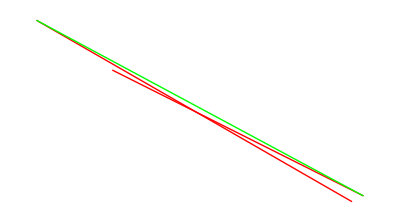

```mathematica
Graphics[{{Red,%799},{Green,%805}}]
```

Instead, get:

```mathematica
{{{Line[{{121.98515386204292,668.3862802694118},{72.58087291135928,696.8154382545846}}],Line[{{123.77047015806056,669.2972475266545},{84.43805191121339,689.0193385632326}}]},{Line[{{209.50450795148635,686.8951352127518},{175.42384655125494,702.5398953107137}}]}}}
```

Make merge lines transparent to this.

Try this on more comples examples

```mathematica
s1=nearbyParallelLines
```

{{{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]},{Line[{{294.9,568.884},{235.095,603.298}}],Line[{{276.1,578.186},{240.809,601.867}}]},{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}],Line[{{209.505,686.895},{175.424,702.54}}]},{Line[{{409.743,569.808},{351.238,603.474}}],Line[{{409.691,567.931},{367.676,595.95}}],Line[{{392.069,581.316},{359.301,597.394}}]},{Line[{{236.828,669.31},{177.023,703.724}}],Line[{{216.895,679.014},{188.639,698.809}}]},{Line[{{308.704,286.034},{359.14,257.395}}],Line[{{316.564,293.024},{358.994,264.728}}],Line[{{315.09,281.19},{346.599,265.952}}],Line[{{412.001,299.489},{439.839,282.717}}]},{Line[{{408.277,303.162},{465.723,263.162}}],Line[{{435.124,285.81},{464.028,262.711}}]},{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]},{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{189.121,122.316},{233.706,113.239}}],Line[{{181.465,126.948},{215.962,115.023}}]},{Line[{{439.649,202.118},{479.81,161.669}}]},{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{277.669,41.9128},{312.201,30.0873}}],Line[{{271.1,41.235},{308.848,33.6631}}]},{Line[{{276.567,159.431},{344.011,142.65}}],Line[{{287.353,150.036},{330.646,136.037}}]}},{{Line[{{408.732,571.518},{409.82,502.526}}]},{Line[{{412.171,353.545},{413.031,299.052}}]},{Line[{{235.898,671.505},{237.011,601.014}}]}},{{Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{573.949,227.168},{528.593,277.832}}],Line[{{551.019,239.366},{531.91,263.776}}]},{Line[{{443.025,201.883},{487.206,150.191}}]}},{{Line[{{360.89,78.3026},{312.349,29.9702}}],Line[{{249.122,49.9212},{227.778,26.0792}}],Line[{{343.168,73.904},{313.82,41.1213}}],Line[{{350.933,78.2382},{325.31,55.8893}}]},{Line[{{278.159,159.78},{230.248,111.525}}],Line[{{267.194,149.811},{245.866,125.288}}],Line[{{272.719,152.113},{244.975,127.633}}]},{Line[{{249.911,48.9246},{201.313,1.36146}}]},{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{401.619,298.92},{372.103,274.2}}],Line[{{375.285,279.829},{413.917,303.866}}]},{Line[{{248.399,475.992},{294.733,503.727}}],Line[{{247.168,477.244},{296.781,502.12}}]},{Line[{{350.933,468.511},{409.708,503.693}}],Line[{{351.366,479.99},{395.679,502.051}}],Line[{{361.809,473.143},{390.59,493.06}}]},{Line[{{293.203,567.697},{352.954,604.165}}],Line[{{292.403,569.319},{345.568,597.132}}],Line[{{324.494,584.948},{351.467,603.96}}]},{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{135.429,669.9},{177.443,690.966}}],Line[{{140.201,679.024},{170.215,699.795}}]},{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{190.289,574.942},{225.497,597.842}}]},{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{82.522,579.151},{115.447,600.973}}]},{Line[{{368.02,182.964},{347.17,151.795}}]}},{{Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{230.405,113.831},{249.785,47.0879}}]},{Line[{{341.657,144.053},{351.91,114.798}}]}},{{Line[{{352.157,471.012},{351.605,416.015}}]}},{{Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{242.699,106.849},{254.387,55.1542}}]}},{{Line[{{294.298,571.018},{293.193,501.027}}]}},{{Line[{{228.772,664.532},{226.944,613.565}}]}},{{Line[{{487.492,150.103},{553.924,164.622}}],Line[{{502.944,160.952},{534.648,170.109}}]},{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{474.461,266.822},{509.552,272.199}}],Line[{{468.053,262.983},{498.745,272.038}}]},{Line[{{392.767,200.04},{444.736,201.83}}],Line[{{392.683,202.009},{444.641,199.921}}]},{Line[{{85.3089,583.804},{124.127,602.302}}]},{Line[{{197.065,581.699},{227.8,596.238}}]}},{{Line[{{464.496,265.047},{442.64,199.073}}]},{Line[{{573.636,230.022},{553.395,162.491}}],Line[{{569.01,210.074},{551.259,163.331}}]}},{{Line[{{120.073,671.516},{121.995,601.042}}]}},{{Line[{{355.455,269.939},{361.986,240.659}}]}},{{Line[{{350.715,471.653},{353.09,439.24}}]}},{{Line[{{300.942,556.2},{303.074,513.754}}]}},{{Line[{{366.296,183.739},{342.773,141.326}}],Line[{{359.29,172.703},{345.862,144.208}}]}},{{Line[{{122.085,656.044},{119.936,600.586}}]}},{{Line[{{465.981,250.339},{454.689,205.231}}]},{Line[{{562.997,199.406},{556.051,168.682}}]}},{{Line[{{413.994,353.456},{411.937,312.508}}]}},{{Line[{{461.039,250.841},{446.925,216.098}}]}}}

## Merge intersecting lines

### Clean

```mathematica
singlesA=Cases[intersectingNearbyParallelLinesByAngle,{_Line},{4}];
```

This takes care of the sets of pairs of intersecting lines.

```mathematica
mergeA1=Cases[intersectingNearbyParallelLinesByAngle,{{Repeated[_Line,{2}]}..},{3}]
```

{{{Line[{{76.3855,578.895},{112.544,595.999}}],Line[{{76.4296,578.105},{123.976,602.632}}]},{Line[{{76.3855,578.895},{112.544,595.999}}],Line[{{77.0837,577.665},{121.94,602.966}}]},{Line[{{76.3855,578.895},{112.544,595.999}}],Line[{{78.1022,577.191},{122.061,604.021}}]},{Line[{{76.4296,578.105},{123.976,602.632}}],Line[{{77.0837,577.665},{121.94,602.966}}]},{Line[{{76.4296,578.105},{123.976,602.632}}],Line[{{78.1022,577.191},{122.061,604.021}}]}},{{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{78.1022,577.191},{122.061,604.021}}]}},{{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{181.702,570.113},{236.854,603.557}}]}},{{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{248.024,476.696},{296.312,503.026}}]},{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{248.399,475.992},{294.733,503.727}}]},{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{260.351,481.938},{294.784,504.194}}]},{Line[{{248.024,476.696},{296.312,503.026}}],Line[{{248.399,475.992},{294.733,503.727}}]},{Line[{{248.024,476.696},{296.312,503.026}}],Line[{{260.351,481.938},{294.784,504.194}}]}},{{Line[{{248.399,475.992},{294.733,503.727}}],Line[{{260.351,481.938},{294.784,504.194}}]}},{{Line[{{292.311,569.332},{331.644,589.054}}],Line[{{292.754,568.779},{354.455,602.884}}]},{Line[{{292.311,569.332},{331.644,589.054}}],Line[{{293.203,567.697},{352.954,604.165}}]},{Line[{{292.754,568.779},{354.455,602.884}}],Line[{{293.203,567.697},{352.954,604.165}}]}},{{Line[{{350.933,468.511},{409.708,503.693}}],Line[{{356.512,470.167},{409.842,504.637}}]}},{{Line[{{351.366,479.99},{395.679,502.051}}],Line[{{351.83,479.008},{401.716,506.582}}]}},{{Line[{{104.624,680.003},{72.3966,696.047}}],Line[{{121.985,668.386},{72.5809,696.815}}]},{Line[{{104.624,680.003},{72.3966,696.047}}],Line[{{123.164,669.158},{72.0835,696.632}}]},{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.164,669.158},{72.0835,696.632}}]}},{{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{120.319,605.069},{168.7,573.994}}]}},{{Line[{{128.621,606.802},{178.665,579.514}}],Line[{{129.674,607.912},{177.136,578.191}}]},{Line[{{128.621,606.802},{178.665,579.514}}],Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{129.674,607.912},{177.136,578.191}}],Line[{{135.175,602.152},{177.697,580.983}}]}},{{Line[{{230.793,674.652},{175.45,702.601}}],Line[{{236.758,667.8},{181.445,702.881}}]},{Line[{{230.793,674.652},{175.45,702.601}}],Line[{{236.828,669.31},{177.023,703.724}}]},{Line[{{236.758,667.8},{181.445,702.881}}],Line[{{236.828,669.31},{177.023,703.724}}]}},{{Line[{{276.1,578.186},{240.809,601.867}}],Line[{{294.649,567.9},{235.215,604.881}}]},{Line[{{276.1,578.186},{240.809,601.867}}],Line[{{294.9,568.884},{235.095,603.298}}]},{Line[{{294.649,567.9},{235.215,604.881}}],Line[{{294.9,568.884},{235.095,603.298}}]}},{{Line[{{292.404,502.374},{354.684,469.336}}],Line[{{292.959,504.148},{354.064,468.985}}]},{Line[{{292.404,502.374},{354.684,469.336}}],Line[{{305.115,498.05},{353.001,468.064}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{305.115,498.05},{353.001,468.064}}]}},{{Line[{{308.314,285.591},{336.711,271.958}}],Line[{{308.704,286.034},{359.14,257.395}}]}},{{Line[{{312.34,292.339},{361.96,266.38}}],Line[{{314.417,293.862},{360.003,265.859}}]},{Line[{{312.34,292.339},{361.96,266.38}}],Line[{{316.564,293.024},{358.994,264.728}}]},{Line[{{314.417,293.862},{360.003,265.859}}],Line[{{316.564,293.024},{358.994,264.728}}]}},{{Line[{{366.271,393.914},{396.027,377.466}}],Line[{{366.507,392.996},{396.006,378.205}}]},{Line[{{366.271,393.914},{396.027,377.466}}],Line[{{367.679,393.98},{395.468,377.128}}]},{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]}},{{Line[{{403.963,304.78},{451.834,273.838}}],Line[{{408.277,303.162},{465.723,263.162}}]}},{{Line[{{120.073,671.516},{121.995,601.042}}],Line[{{122.035,671.02},{119.897,600.052}}]}},{{Line[{{228.289,665.},{228.207,608.}}],Line[{{228.772,664.532},{226.944,613.565}}]}},{{Line[{{234.938,652.579},{237.071,610.132}}],Line[{{235.898,671.505},{237.011,601.014}}]}},{{Line[{{292.921,547.188},{295.098,501.24}}],Line[{{294.298,571.018},{293.193,501.027}}]}},{{Line[{{300.921,561.266},{303.066,524.829}}],Line[{{301.276,564.513},{302.006,508.017}}]},{Line[{{300.921,561.266},{303.066,524.829}}],Line[{{303.09,560.695},{300.931,517.749}}]},{Line[{{301.276,564.513},{302.006,508.017}}],Line[{{303.09,560.695},{300.931,517.749}}]}},{{Line[{{350.715,471.653},{353.09,439.24}}],Line[{{351.255,471.073},{352.596,416.089}}]},{Line[{{350.715,471.653},{353.09,439.24}}],Line[{{352.157,471.012},{351.605,416.015}}]},{Line[{{350.715,471.653},{353.09,439.24}}],Line[{{353.06,470.742},{350.927,422.789}}]},{Line[{{351.255,471.073},{352.596,416.089}}],Line[{{352.157,471.012},{351.605,416.015}}]},{Line[{{351.255,471.073},{352.596,416.089}}],Line[{{353.06,470.742},{350.927,422.789}}]}},{{Line[{{352.157,471.012},{351.605,416.015}}],Line[{{353.06,470.742},{350.927,422.789}}]}},{{Line[{{407.897,562.692},{410.105,518.748}}],Line[{{408.732,571.518},{409.82,502.526}}]},{Line[{{407.897,562.692},{410.105,518.748}}],Line[{{409.69,570.533},{408.195,501.05}}]},{Line[{{408.732,571.518},{409.82,502.526}}],Line[{{409.69,570.533},{408.195,501.05}}]}},{{Line[{{166.403,128.742},{233.062,112.966}}],Line[{{167.361,129.318},{232.954,111.389}}]}},{{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{253.35,46.3482},{315.226,32.0786}}]}},{{Line[{{276.567,159.431},{344.011,142.65}}],Line[{{279.093,160.089},{344.903,141.082}}]}},{{Line[{{230.405,113.831},{249.785,47.0879}}],Line[{{231.288,113.995},{248.237,47.1088}}]},{Line[{{230.405,113.831},{249.785,47.0879}}],Line[{{237.676,93.9249},{245.41,56.2098}}]},{Line[{{231.288,113.995},{248.237,47.1088}}],Line[{{237.676,93.9249},{245.41,56.2098}}]}},{{Line[{{241.045,103.568},{256.009,57.9602}}],Line[{{241.132,109.856},{254.264,55.4178}}]}},{{Line[{{341.657,144.053},{351.91,114.798}}],Line[{{342.042,143.629},{358.998,87.6404}}]},{Line[{{341.657,144.053},{351.91,114.798}}],Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{341.657,144.053},{351.91,114.798}}],Line[{{346.765,134.647},{356.289,90.1549}}]},{Line[{{342.042,143.629},{358.998,87.6404}}],Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{342.042,143.629},{358.998,87.6404}}],Line[{{346.765,134.647},{356.289,90.1549}}]}},{{Line[{{343.381,144.53},{360.452,77.159}}],Line[{{346.765,134.647},{356.289,90.1549}}]}},{{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{354.604,269.676},{370.955,214.549}}]},{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{361.749,249.906},{370.918,214.576}}]},{Line[{{354.604,269.676},{370.955,214.549}}],Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{354.604,269.676},{370.955,214.549}}],Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{354.604,269.676},{370.955,214.549}}],Line[{{361.749,249.906},{370.918,214.576}}]}},{{Line[{{355.154,265.002},{371.966,214.739}}],Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{355.154,265.002},{371.966,214.739}}],Line[{{361.749,249.906},{370.918,214.576}}]}},{{Line[{{241.06,41.748},{202.527,1.11322}}],Line[{{249.911,48.9246},{201.313,1.36146}}]},{Line[{{241.06,41.748},{202.527,1.11322}}],Line[{{250.509,48.8124},{223.191,23.858}}]},{Line[{{249.911,48.9246},{201.313,1.36146}}],Line[{{250.509,48.8124},{223.191,23.858}}]}},{{Line[{{271.092,153.755},{231.113,110.365}}],Line[{{275.826,155.168},{229.926,112.015}}]},{Line[{{271.092,153.755},{231.113,110.365}}],Line[{{278.159,159.78},{230.248,111.525}}]},{Line[{{275.826,155.168},{229.926,112.015}}],Line[{{278.159,159.78},{230.248,111.525}}]}},{{Line[{{343.168,73.904},{313.82,41.1213}}],Line[{{350.875,80.8307},{310.947,40.1516}}]}},{{Line[{{357.9,74.3107},{310.288,30.0604}}],Line[{{360.852,80.4241},{325.726,42.0815}}]},{Line[{{357.9,74.3107},{310.288,30.0604}}],Line[{{360.89,78.3026},{312.349,29.9702}}]},{Line[{{360.852,80.4241},{325.726,42.0815}}],Line[{{360.89,78.3026},{312.349,29.9702}}]}},{{Line[{{401.619,298.92},{372.103,274.2}}],Line[{{408.78,303.829},{352.561,260.466}}]}},{{Line[{{366.296,183.739},{342.773,141.326}}],Line[{{367.815,183.576},{341.988,141.935}}]}},{{Line[{{392.,201.286},{445.,201.286}}],Line[{{392.683,202.009},{444.641,199.921}}]},{Line[{{392.,201.286},{445.,201.286}}],Line[{{392.767,200.04},{444.736,201.83}}]},{Line[{{392.683,202.009},{444.641,199.921}}],Line[{{392.767,200.04},{444.736,201.83}}]}},{{Line[{{409.684,303.944},{463.883,262.878}}],Line[{{417.375,298.917},{451.51,271.153}}]}},{{Line[{{440.765,201.944},{488.388,149.96}}],Line[{{443.025,201.883},{487.206,150.191}}]}},{{Line[{{576.229,137.173},{556.74,161.921}}],Line[{{588.64,124.03},{553.025,165.942}}]},{Line[{{576.229,137.173},{556.74,161.921}}],Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{588.64,124.03},{553.025,165.942}}],Line[{{588.956,124.609},{551.572,164.95}}]}},{{Line[{{461.607,264.162},{530.431,276.943}}],Line[{{462.288,262.764},{529.655,277.69}}]}},{{Line[{{573.636,230.022},{553.395,162.491}}],Line[{{574.114,227.877},{552.014,163.04}}]}}}

```mathematica
mAOLD=Cases[intersectingNearbyParallelLinesByAngle,{Repeated[_Line,{2}]..},{4}]
```

{{Line[{{76.3855,578.895},{112.544,595.999}}],Line[{{76.4296,578.105},{123.976,602.632}}]},{Line[{{76.3855,578.895},{112.544,595.999}}],Line[{{77.0837,577.665},{121.94,602.966}}]},{Line[{{76.3855,578.895},{112.544,595.999}}],Line[{{78.1022,577.191},{122.061,604.021}}]},{Line[{{76.4296,578.105},{123.976,602.632}}],Line[{{77.0837,577.665},{121.94,602.966}}]},{Line[{{76.4296,578.105},{123.976,602.632}}],Line[{{78.1022,577.191},{122.061,604.021}}]},{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{78.1022,577.191},{122.061,604.021}}]},{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{120.124,667.632},{180.186,703.584}}]},{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{125.136,669.97},{177.626,703.897}}]},{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{125.136,669.97},{177.626,703.897}}]},{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{181.702,570.113},{236.854,603.557}}]},{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{248.024,476.696},{296.312,503.026}}]},{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{248.399,475.992},{294.733,503.727}}]},{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{260.351,481.938},{294.784,504.194}}]},{Line[{{248.024,476.696},{296.312,503.026}}],Line[{{248.399,475.992},{294.733,503.727}}]},{Line[{{248.024,476.696},{296.312,503.026}}],Line[{{260.351,481.938},{294.784,504.194}}]},{Line[{{248.399,475.992},{294.733,503.727}}],Line[{{260.351,481.938},{294.784,504.194}}]},{Line[{{292.311,569.332},{331.644,589.054}}],Line[{{292.754,568.779},{354.455,602.884}}]},{Line[{{292.311,569.332},{331.644,589.054}}],Line[{{293.203,567.697},{352.954,604.165}}]},{Line[{{292.754,568.779},{354.455,602.884}}],Line[{{293.203,567.697},{352.954,604.165}}]},{Line[{{350.933,468.511},{409.708,503.693}}],Line[{{356.512,470.167},{409.842,504.637}}]},{Line[{{351.366,479.99},{395.679,502.051}}],Line[{{351.83,479.008},{401.716,506.582}}]},{Line[{{104.624,680.003},{72.3966,696.047}}],Line[{{121.985,668.386},{72.5809,696.815}}]},{Line[{{104.624,680.003},{72.3966,696.047}}],Line[{{123.164,669.158},{72.0835,696.632}}]},{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.164,669.158},{72.0835,696.632}}]},{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{120.319,605.069},{168.7,573.994}}]},{Line[{{128.621,606.802},{178.665,579.514}}],Line[{{129.674,607.912},{177.136,578.191}}]},{Line[{{128.621,606.802},{178.665,579.514}}],Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{129.674,607.912},{177.136,578.191}}],Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{230.793,674.652},{175.45,702.601}}],Line[{{236.758,667.8},{181.445,702.881}}]},{Line[{{230.793,674.652},{175.45,702.601}}],Line[{{236.828,669.31},{177.023,703.724}}]},{Line[{{236.758,667.8},{181.445,702.881}}],Line[{{236.828,669.31},{177.023,703.724}}]},{Line[{{276.1,578.186},{240.809,601.867}}],Line[{{294.649,567.9},{235.215,604.881}}]},{Line[{{276.1,578.186},{240.809,601.867}}],Line[{{294.9,568.884},{235.095,603.298}}]},{Line[{{294.649,567.9},{235.215,604.881}}],Line[{{294.9,568.884},{235.095,603.298}}]},{Line[{{292.404,502.374},{354.684,469.336}}],Line[{{292.959,504.148},{354.064,468.985}}]},{Line[{{292.404,502.374},{354.684,469.336}}],Line[{{305.115,498.05},{353.001,468.064}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{305.115,498.05},{353.001,468.064}}]},{Line[{{308.314,285.591},{336.711,271.958}}],Line[{{308.704,286.034},{359.14,257.395}}]},{Line[{{312.34,292.339},{361.96,266.38}}],Line[{{314.417,293.862},{360.003,265.859}}]},{Line[{{312.34,292.339},{361.96,266.38}}],Line[{{316.564,293.024},{358.994,264.728}}]},{Line[{{314.417,293.862},{360.003,265.859}}],Line[{{316.564,293.024},{358.994,264.728}}]},{Line[{{366.271,393.914},{396.027,377.466}}],Line[{{366.507,392.996},{396.006,378.205}}]},{Line[{{366.271,393.914},{396.027,377.466}}],Line[{{367.679,393.98},{395.468,377.128}}]},{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]},{Line[{{403.567,574.93},{359.318,597.117}}],Line[{{409.743,569.808},{351.238,603.474}}]},{Line[{{403.963,304.78},{451.834,273.838}}],Line[{{408.277,303.162},{465.723,263.162}}]},{Line[{{120.073,671.516},{121.995,601.042}}],Line[{{122.035,671.02},{119.897,600.052}}]},{Line[{{228.289,665.},{228.207,608.}}],Line[{{228.772,664.532},{226.944,613.565}}]},{Line[{{234.938,652.579},{237.071,610.132}}],Line[{{235.898,671.505},{237.011,601.014}}]},{Line[{{292.921,547.188},{295.098,501.24}}],Line[{{294.298,571.018},{293.193,501.027}}]},{Line[{{300.921,561.266},{303.066,524.829}}],Line[{{301.276,564.513},{302.006,508.017}}]},{Line[{{300.921,561.266},{303.066,524.829}}],Line[{{303.09,560.695},{300.931,517.749}}]},{Line[{{301.276,564.513},{302.006,508.017}}],Line[{{303.09,560.695},{300.931,517.749}}]},{Line[{{350.715,471.653},{353.09,439.24}}],Line[{{351.255,471.073},{352.596,416.089}}]},{Line[{{350.715,471.653},{353.09,439.24}}],Line[{{352.157,471.012},{351.605,416.015}}]},{Line[{{350.715,471.653},{353.09,439.24}}],Line[{{353.06,470.742},{350.927,422.789}}]},{Line[{{351.255,471.073},{352.596,416.089}}],Line[{{352.157,471.012},{351.605,416.015}}]},{Line[{{351.255,471.073},{352.596,416.089}}],Line[{{353.06,470.742},{350.927,422.789}}]},{Line[{{352.157,471.012},{351.605,416.015}}],Line[{{353.06,470.742},{350.927,422.789}}]},{Line[{{403.949,341.971},{406.107,299.025}}],Line[{{405.021,353.584},{403.956,304.095}}]},{Line[{{407.897,562.692},{410.105,518.748}}],Line[{{408.732,571.518},{409.82,502.526}}]},{Line[{{407.897,562.692},{410.105,518.748}}],Line[{{409.69,570.533},{408.195,501.05}}]},{Line[{{408.732,571.518},{409.82,502.526}}],Line[{{409.69,570.533},{408.195,501.05}}]},{Line[{{166.403,128.742},{233.062,112.966}}],Line[{{167.361,129.318},{232.954,111.389}}]},{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{253.35,46.3482},{315.226,32.0786}}]},{Line[{{276.567,159.431},{344.011,142.65}}],Line[{{279.093,160.089},{344.903,141.082}}]},{Line[{{230.405,113.831},{249.785,47.0879}}],Line[{{231.288,113.995},{248.237,47.1088}}]},{Line[{{230.405,113.831},{249.785,47.0879}}],Line[{{237.676,93.9249},{245.41,56.2098}}]},{Line[{{231.288,113.995},{248.237,47.1088}}],Line[{{237.676,93.9249},{245.41,56.2098}}]},{Line[{{241.045,103.568},{256.009,57.9602}}],Line[{{241.132,109.856},{254.264,55.4178}}]},{Line[{{341.657,144.053},{351.91,114.798}}],Line[{{342.042,143.629},{358.998,87.6404}}]},{Line[{{341.657,144.053},{351.91,114.798}}],Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{341.657,144.053},{351.91,114.798}}],Line[{{346.765,134.647},{356.289,90.1549}}]},{Line[{{342.042,143.629},{358.998,87.6404}}],Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{342.042,143.629},{358.998,87.6404}}],Line[{{346.765,134.647},{356.289,90.1549}}]},{Line[{{343.381,144.53},{360.452,77.159}}],Line[{{346.765,134.647},{356.289,90.1549}}]},{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{354.604,269.676},{370.955,214.549}}]},{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{354.346,264.829},{370.955,220.327}}],Line[{{361.749,249.906},{370.918,214.576}}]},{Line[{{354.604,269.676},{370.955,214.549}}],Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{354.604,269.676},{370.955,214.549}}],Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{354.604,269.676},{370.955,214.549}}],Line[{{361.749,249.906},{370.918,214.576}}]},{Line[{{355.154,265.002},{371.966,214.739}}],Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{355.154,265.002},{371.966,214.739}}],Line[{{361.749,249.906},{370.918,214.576}}]},{Line[{{241.06,41.748},{202.527,1.11322}}],Line[{{249.911,48.9246},{201.313,1.36146}}]},{Line[{{241.06,41.748},{202.527,1.11322}}],Line[{{250.509,48.8124},{223.191,23.858}}]},{Line[{{249.911,48.9246},{201.313,1.36146}}],Line[{{250.509,48.8124},{223.191,23.858}}]},{Line[{{271.092,153.755},{231.113,110.365}}],Line[{{275.826,155.168},{229.926,112.015}}]},{Line[{{271.092,153.755},{231.113,110.365}}],Line[{{278.159,159.78},{230.248,111.525}}]},{Line[{{275.826,155.168},{229.926,112.015}}],Line[{{278.159,159.78},{230.248,111.525}}]},{Line[{{343.168,73.904},{313.82,41.1213}}],Line[{{350.875,80.8307},{310.947,40.1516}}]},{Line[{{357.9,74.3107},{310.288,30.0604}}],Line[{{360.852,80.4241},{325.726,42.0815}}]},{Line[{{357.9,74.3107},{310.288,30.0604}}],Line[{{360.89,78.3026},{312.349,29.9702}}]},{Line[{{360.852,80.4241},{325.726,42.0815}}],Line[{{360.89,78.3026},{312.349,29.9702}}]},{Line[{{401.619,298.92},{372.103,274.2}}],Line[{{408.78,303.829},{352.561,260.466}}]},{Line[{{366.296,183.739},{342.773,141.326}}],Line[{{367.815,183.576},{341.988,141.935}}]},{Line[{{392.,201.286},{445.,201.286}}],Line[{{392.683,202.009},{444.641,199.921}}]},{Line[{{392.,201.286},{445.,201.286}}],Line[{{392.767,200.04},{444.736,201.83}}]},{Line[{{392.683,202.009},{444.641,199.921}}],Line[{{392.767,200.04},{444.736,201.83}}]},{Line[{{409.684,303.944},{463.883,262.878}}],Line[{{417.375,298.917},{451.51,271.153}}]},{Line[{{440.765,201.944},{488.388,149.96}}],Line[{{443.025,201.883},{487.206,150.191}}]},{Line[{{569.152,231.238},{539.871,266.716}}],Line[{{573.949,227.168},{528.593,277.832}}]},{Line[{{576.229,137.173},{556.74,161.921}}],Line[{{588.64,124.03},{553.025,165.942}}]},{Line[{{576.229,137.173},{556.74,161.921}}],Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{588.64,124.03},{553.025,165.942}}],Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{461.607,264.162},{530.431,276.943}}],Line[{{462.288,262.764},{529.655,277.69}}]},{Line[{{490.393,160.551},{547.015,170.563}}],Line[{{492.741,159.011},{543.615,171.98}}]},{Line[{{463.17,264.981},{443.598,198.293}}],Line[{{464.496,265.047},{442.64,199.073}}]},{Line[{{573.636,230.022},{553.395,162.491}}],Line[{{574.114,227.877},{552.014,163.04}}]}}

This takes care of their being a pair of intersecting lines and a lone line in its own list.

```mathematica
mergeA2Prelim=Cases[intersectingNearbyParallelLinesByAngle,{Repeated[{Repeated[_Line,{2}]},{1,Infinity}],Repeated[{_Line},{1,Infinity}]},{3}]
```

{{{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{120.124,667.632},{180.186,703.584}}]},{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{125.136,669.97},{177.626,703.897}}]},{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{125.136,669.97},{177.626,703.897}}]},{Line[{{135.429,669.9},{177.443,690.966}}]}},{{Line[{{403.567,574.93},{359.318,597.117}}],Line[{{409.743,569.808},{351.238,603.474}}]},{Line[{{398.899,564.968},{353.297,593.889}}]}},{{Line[{{403.949,341.971},{406.107,299.025}}],Line[{{405.021,353.584},{403.956,304.095}}]},{Line[{{412.171,353.545},{413.031,299.052}}]}},{{Line[{{569.152,231.238},{539.871,266.716}}],Line[{{573.949,227.168},{528.593,277.832}}]},{Line[{{564.838,226.187},{525.537,268.841}}]}},{{Line[{{490.393,160.551},{547.015,170.563}}],Line[{{492.741,159.011},{543.615,171.98}}]},{Line[{{487.492,150.103},{553.924,164.622}}]}},{{Line[{{463.17,264.981},{443.598,198.293}}],Line[{{464.496,265.047},{442.64,199.073}}]},{Line[{{465.981,250.339},{454.689,205.231}}]}}}

```mathematica
mergeA2=DeleteCases[mergeA2Prelim,{_Line},{2}]
```

{{{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{120.124,667.632},{180.186,703.584}}]},{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{125.136,669.97},{177.626,703.897}}]},{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{125.136,669.97},{177.626,703.897}}]}},{{Line[{{403.567,574.93},{359.318,597.117}}],Line[{{409.743,569.808},{351.238,603.474}}]}},{{Line[{{403.949,341.971},{406.107,299.025}}],Line[{{405.021,353.584},{403.956,304.095}}]}},{{Line[{{569.152,231.238},{539.871,266.716}}],Line[{{573.949,227.168},{528.593,277.832}}]}},{{Line[{{490.393,160.551},{547.015,170.563}}],Line[{{492.741,159.011},{543.615,171.98}}]}},{{Line[{{463.17,264.981},{443.598,198.293}}],Line[{{464.496,265.047},{442.64,199.073}}]}}}

```mathematica
(*mergeA2=Cases[mergeA2Prelim,{_Line,_Line},{2}]*)
```

{{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{120.124,667.632},{180.186,703.584}}]},{Line[{{119.842,669.13},{172.08,697.615}}],Line[{{125.136,669.97},{177.626,703.897}}]},{Line[{{120.124,667.632},{180.186,703.584}}],Line[{{125.136,669.97},{177.626,703.897}}]},{Line[{{403.567,574.93},{359.318,597.117}}],Line[{{409.743,569.808},{351.238,603.474}}]},{Line[{{403.949,341.971},{406.107,299.025}}],Line[{{405.021,353.584},{403.956,304.095}}]},{Line[{{569.152,231.238},{539.871,266.716}}],Line[{{573.949,227.168},{528.593,277.832}}]},{Line[{{490.393,160.551},{547.015,170.563}}],Line[{{492.741,159.011},{543.615,171.98}}]},{Line[{{463.17,264.981},{443.598,198.293}}],Line[{{464.496,265.047},{442.64,199.073}}]}}

```mathematica
mergeA=Join[mergeA1,mergeA2];
```

```mathematica
mergedIntersectingNearbyParallelLinesByAngle= Map[mergeLines,mergeA,{1}];
```

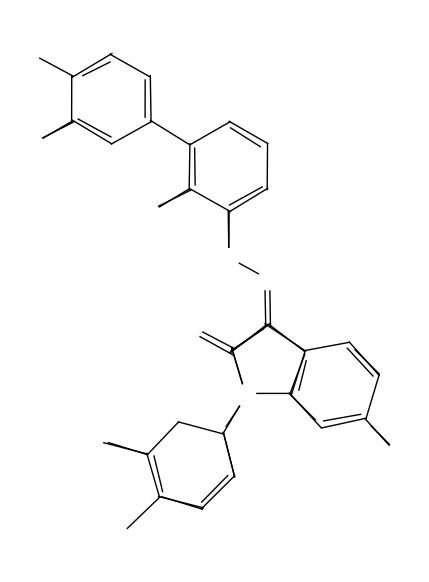

```mathematica
cleanLines=Flatten@Join[singlesA,mergedIntersectingNearbyParallelLinesByAngle];
Graphics[cleanLines]
```

### Tests

#### Get the single lines.

```mathematica
singlesA=Cases[intersectingNearbyParallelLinesByAngle,{_Line},{4}]
```

{{Line[{{135.429,669.9},{177.443,690.966}}]},{Line[{{351.366,479.99},{395.679,502.051}}]},{Line[{{120.044,603.65},{179.849,569.236}}]},{Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{316.564,293.024},{358.994,264.728}}]},{Line[{{228.772,664.532},{226.944,613.565}}]},{Line[{{235.898,671.505},{237.011,601.014}}]},{Line[{{294.298,571.018},{293.193,501.027}}]},{Line[{{300.942,556.2},{303.074,513.754}}]},{Line[{{408.732,571.518},{409.82,502.526}}]},{Line[{{276.567,159.431},{344.011,142.65}}]},{Line[{{287.353,150.036},{330.646,136.037}}]},{Line[{{230.405,113.831},{249.785,47.0879}}]},{Line[{{242.699,106.849},{254.387,55.1542}}]},{Line[{{360.89,78.3026},{312.349,29.9702}}]},{Line[{{368.02,182.964},{347.17,151.795}}]},{Line[{{401.619,298.92},{372.103,274.2}}]},{Line[{{551.019,239.366},{531.91,263.776}}]},{Line[{{573.949,227.168},{528.593,277.832}}]},{Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{487.492,150.103},{553.924,164.622}}]},{Line[{{502.944,160.952},{534.648,170.109}}]},{Line[{{465.981,250.339},{454.689,205.231}}]},{Line[{{562.997,199.406},{556.051,168.682}}]}}

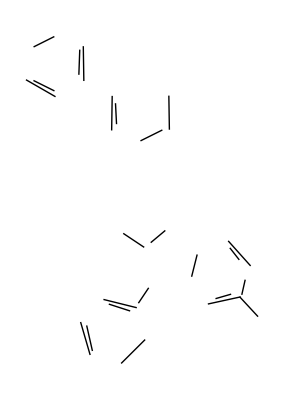

```mathematica
Graphics[%]
```

#### Get the sets of lines to be merged.

```mathematica
mA=Cases[intersectingNearbyParallelLinesByAngle,{{Repeated[_Line,{2}]}..},{3}]
```

{{{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{82.522,579.151},{115.447,600.973}}]},{Line[{{77.0837,577.665},{121.94,602.966}}],Line[{{85.3089,583.804},{124.127,602.302}}]},{Line[{{82.522,579.151},{115.447,600.973}}],Line[{{85.3089,583.804},{124.127,602.302}}]}},{{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{190.289,574.942},{225.497,597.842}}]},{Line[{{177.535,568.914},{238.167,602.884}}],Line[{{197.065,581.699},{227.8,596.238}}]},{Line[{{190.289,574.942},{225.497,597.842}}],Line[{{197.065,581.699},{227.8,596.238}}]}},{{Line[{{247.168,477.244},{296.781,502.12}}],Line[{{248.399,475.992},{294.733,503.727}}]}},{{Line[{{292.403,569.319},{345.568,597.132}}],Line[{{293.203,567.697},{352.954,604.165}}]},{Line[{{292.403,569.319},{345.568,597.132}}],Line[{{324.494,584.948},{351.467,603.96}}]},{Line[{{293.203,567.697},{352.954,604.165}}],Line[{{324.494,584.948},{351.467,603.96}}]}},{{Line[{{352.165,260.943},{413.906,305.261}}],Line[{{375.285,279.829},{413.917,303.866}}]}},{{Line[{{121.985,668.386},{72.5809,696.815}}],Line[{{123.77,669.297},{84.4381,689.019}}]}},{{Line[{{209.505,686.895},{175.424,702.54}}],Line[{{216.895,679.014},{188.639,698.809}}]},{Line[{{209.505,686.895},{175.424,702.54}}],Line[{{236.828,669.31},{177.023,703.724}}]},{Line[{{216.895,679.014},{188.639,698.809}}],Line[{{236.828,669.31},{177.023,703.724}}]}},{{Line[{{276.1,578.186},{240.809,601.867}}],Line[{{294.9,568.884},{235.095,603.298}}]}},{{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{317.396,491.066},{352.754,467.486}}]},{Line[{{292.959,504.148},{354.064,468.985}}],Line[{{322.29,485.05},{354.609,469.192}}]},{Line[{{317.396,491.066},{352.754,467.486}}],Line[{{322.29,485.05},{354.609,469.192}}]}},{{Line[{{366.507,392.996},{396.006,378.205}}],Line[{{367.679,393.98},{395.468,377.128}}]}},{{Line[{{392.069,581.316},{359.301,597.394}}],Line[{{409.691,567.931},{367.676,595.95}}]},{Line[{{392.069,581.316},{359.301,597.394}}],Line[{{409.743,569.808},{351.238,603.474}}]},{Line[{{409.691,567.931},{367.676,595.95}}],Line[{{409.743,569.808},{351.238,603.474}}]}},{{Line[{{408.277,303.162},{465.723,263.162}}],Line[{{412.001,299.489},{439.839,282.717}}]},{Line[{{408.277,303.162},{465.723,263.162}}],Line[{{435.124,285.81},{464.028,262.711}}]},{Line[{{412.001,299.489},{439.839,282.717}}],Line[{{435.124,285.81},{464.028,262.711}}]}},{{Line[{{120.073,671.516},{121.995,601.042}}],Line[{{122.085,656.044},{119.936,600.586}}]}},{{Line[{{350.715,471.653},{353.09,439.24}}],Line[{{352.157,471.012},{351.605,416.015}}]}},{{Line[{{412.171,353.545},{413.031,299.052}}],Line[{{413.994,353.456},{411.937,312.508}}]}},{{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{181.465,126.948},{215.962,115.023}}]},{Line[{{167.361,129.318},{232.954,111.389}}],Line[{{189.121,122.316},{233.706,113.239}}]},{Line[{{181.465,126.948},{215.962,115.023}}],Line[{{189.121,122.316},{233.706,113.239}}]}},{{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{271.1,41.235},{308.848,33.6631}}]},{Line[{{247.134,49.3561},{314.71,31.0933}}],Line[{{277.669,41.9128},{312.201,30.0873}}]},{Line[{{271.1,41.235},{308.848,33.6631}}],Line[{{277.669,41.9128},{312.201,30.0873}}]}},{{Line[{{341.657,144.053},{351.91,114.798}}],Line[{{343.381,144.53},{360.452,77.159}}]}},{{Line[{{355.154,265.002},{371.966,214.739}}],Line[{{355.455,269.939},{361.986,240.659}}]}},{{Line[{{249.122,49.9212},{227.778,26.0792}}],Line[{{249.911,48.9246},{201.313,1.36146}}]}},{{Line[{{267.194,149.811},{245.866,125.288}}],Line[{{272.719,152.113},{244.975,127.633}}]},{Line[{{267.194,149.811},{245.866,125.288}}],Line[{{278.159,159.78},{230.248,111.525}}]},{Line[{{272.719,152.113},{244.975,127.633}}],Line[{{278.159,159.78},{230.248,111.525}}]}},{{Line[{{359.29,172.703},{345.862,144.208}}],Line[{{366.296,183.739},{342.773,141.326}}]}},{{Line[{{461.039,250.841},{446.925,216.098}}],Line[{{464.496,265.047},{442.64,199.073}}]}},{{Line[{{569.01,210.074},{551.259,163.331}}],Line[{{573.636,230.022},{553.395,162.491}}]}},{{Line[{{392.683,202.009},{444.641,199.921}}],Line[{{392.767,200.04},{444.736,201.83}}]}},{{Line[{{439.649,202.118},{479.81,161.669}}],Line[{{443.025,201.883},{487.206,150.191}}]}},{{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{468.053,262.983},{498.745,272.038}}]},{Line[{{462.288,262.764},{529.655,277.69}}],Line[{{474.461,266.822},{509.552,272.199}}]},{Line[{{468.053,262.983},{498.745,272.038}}],Line[{{474.461,266.822},{509.552,272.199}}]}}}

```mathematica
mergedIntersectingNearbyParallelLinesByAngle= Map[mergeLines,mA,{1}];
```

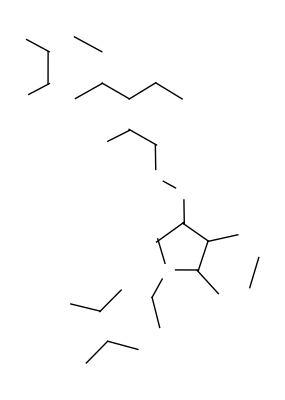

```mathematica
Graphics[mergedIntersectingNearbyParallelLinesByAngle]
```

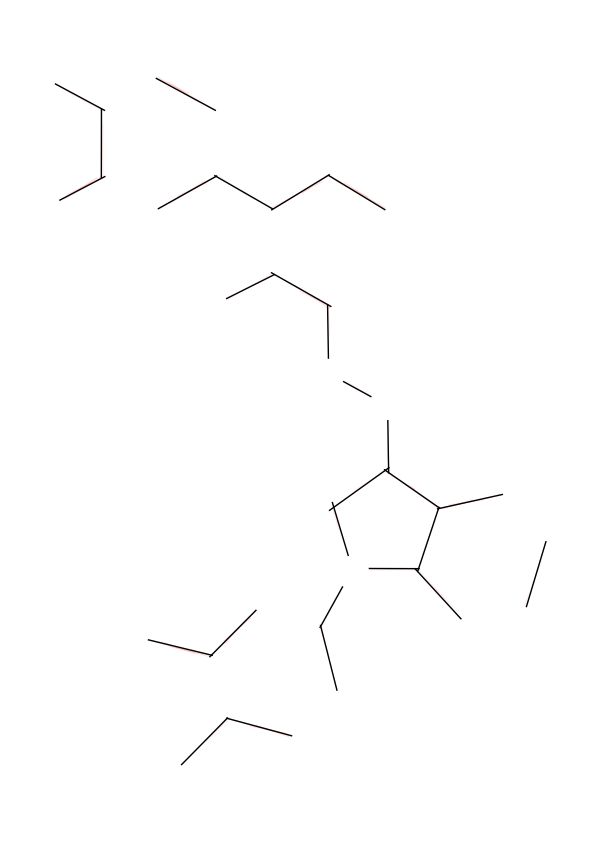

```mathematica
Graphics[{Thick,Red,Opacity[0.05],mA,Thin,Black,Opacity[1],mergedIntersectingNearbyParallelLinesByAngle}]
```

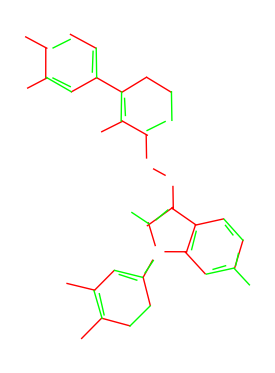

```mathematica
Graphics[{Red,mergedIntersectingNearbyParallelLinesByAngle,Green,singlesA}]
```

Some of the lines are not being marked for merge

#### Angle

```mathematica
nearbyParallelLinesByAngle
```

```mathematica
singlesA
```

{{Line[{{120.044,603.65},{179.849,569.236}}]},{Line[{{135.175,602.152},{177.697,580.983}}]},{Line[{{316.564,293.024},{358.994,264.728}}]},{Line[{{439.649,202.118},{479.81,161.669}}]},{Line[{{276.567,159.431},{344.011,142.65}}]},{Line[{{287.353,150.036},{330.646,136.037}}]},{Line[{{408.732,571.518},{409.82,502.526}}]},{Line[{{412.171,353.545},{413.031,299.052}}]},{Line[{{235.898,671.505},{237.011,601.014}}]},{Line[{{588.956,124.609},{551.572,164.95}}]},{Line[{{551.019,239.366},{531.91,263.776}}]},{Line[{{573.949,227.168},{528.593,277.832}}]},{Line[{{443.025,201.883},{487.206,150.191}}]},{Line[{{360.89,78.3026},{312.349,29.9702}}]},{Line[{{351.366,479.99},{395.679,502.051}}]},{Line[{{135.429,669.9},{177.443,690.966}}]},{Line[{{368.02,182.964},{347.17,151.795}}]},{Line[{{355.154,265.002},{371.966,214.739}}]},{Line[{{230.405,113.831},{249.785,47.0879}}]},{Line[{{341.657,144.053},{351.91,114.798}}]},{Line[{{352.157,471.012},{351.605,416.015}}]},{Line[{{343.381,144.53},{360.452,77.159}}]},{Line[{{242.699,106.849},{254.387,55.1542}}]},{Line[{{294.298,571.018},{293.193,501.027}}]},{Line[{{228.772,664.532},{226.944,613.565}}]},{Line[{{487.492,150.103},{553.924,164.622}}]},{Line[{{502.944,160.952},{534.648,170.109}}]},{Line[{{85.3089,583.804},{124.127,602.302}}]},{Line[{{197.065,581.699},{227.8,596.238}}]},{Line[{{464.496,265.047},{442.64,199.073}}]},{Line[{{120.073,671.516},{121.995,601.042}}]},{Line[{{355.455,269.939},{361.986,240.659}}]},{Line[{{350.715,471.653},{353.09,439.24}}]},{Line[{{300.942,556.2},{303.074,513.754}}]},{Line[{{122.085,656.044},{119.936,600.586}}]},{Line[{{465.981,250.339},{454.689,205.231}}]},{Line[{{562.997,199.406},{556.051,168.682}}]},{Line[{{413.994,353.456},{411.937,312.508}}]},{Line[{{461.039,250.841},{446.925,216.098}}]}}

## Locate and merge vertices

### Current

```mathematica
cleanPoints=Sort@Flatten[First/@cleanLines,1];
```

Also does the merge

```mathematica
Manipulate[Graphics[{Thin,Gray,cleanLines,Black,Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<t&]]]}],{t,1,100}]
```

Distance of 30 looks pretty good for merging

```mathematica
mergedPoints=Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<30&]]];
```

### Tests

```mathematica
i
```

-Graphics-

I need to link the merged point with the original point and the line which it came from.

## Get from an atom position through the edge to the other vertex or vertices

### Current Best

use 42 for image 1493. around 35 for image 10

```mathematica
mergeThreshold=35;
```

```mathematica
cleanPointsGathered=Gather[cleanPoints,EuclideanDistance[#1,#2]<mergeThreshold&];
```

```mathematica
mergedPoints=Point/@Mean/@cleanPointsGathered;
```

```mathematica
mergedPointParents=AssociationThread[mergedPoints,Map[Point,cleanPointsGathered,{2}]];
```

```mathematica
separatePointsChild=Merge[Flatten@Map[Reverse,Thread/@Normal[mergedPointParents],{2}],Identity];
```

### Tests

The merged point in question

```mathematica
pQ=mergedPoints[[1]]
```

Point[{72.0835,696.632}]

```mathematica
pQP=mergedPointParents[pQ]
```

{Point[{72.0835,696.632}]}

The line that goes with it

NEED TO DO EACH INDEX

```mathematica
pQP[[;;,1]]
```

{{72.0835,696.632}}

```mathematica
nTrace=1;
pointIndex=Position[cleanLines,pQP[[nTrace,1]]]
otherPointIndex=pointIndex;
```

{{24,1,2}}

```mathematica
otherPointIndex[[1,-1]]=Mod[#,2]+1&@pointIndex[[1,-1]];
otherPointIndex
```

{{24,1,1}}

The other point of that line

```mathematica
Part[cleanLines,Sequence@@Flatten@pointIndex]
```

{7.27457,157.134}

```mathematica
otherPoint=Point@Part[cleanLines,Sequence@@Flatten@otherPointIndex]
```

Point[{123.164,669.158}]

The other merged point

```mathematica
separatePointsChild[otherPoint]
```

{Point[{124.697,669.551}]}

Build an edge list from this.

### Tests

#### Point to line

```mathematica
cleanPoints
```

{{135.429,669.9},{177.443,690.966},{351.366,479.99},{395.679,502.051},{120.044,603.65},{179.849,569.236},{135.175,602.152},{177.697,580.983},{316.564,293.024},{358.994,264.728},{228.772,664.532},{226.944,613.565},{235.898,671.505},{237.011,601.014},{294.298,571.018},{293.193,501.027},{300.942,556.2},{303.074,513.754},{408.732,571.518},{409.82,502.526},{276.567,159.431},{344.011,142.65},{287.353,150.036},{330.646,136.037},{230.405,113.831},{249.785,47.0879},{242.699,106.849},{254.387,55.1542},{360.89,78.3026},{312.349,29.9702},{368.02,182.964},{347.17,151.795},{401.619,298.92},{372.103,274.2},{551.019,239.366},{531.91,263.776},{573.949,227.168},{528.593,277.832},{588.956,124.609},{551.572,164.95},{487.492,150.103},{553.924,164.622},{502.944,160.952},{534.648,170.109},{465.981,250.339},{454.689,205.231},{562.997,199.406},{556.051,168.682},{77.0837,577.665},{124.127,602.302},{177.535,568.914},{238.167,602.884},{247.168,477.244},{296.781,502.12},{293.203,567.697},{352.954,604.165},{352.165,260.943},{413.906,305.261},{72.5809,696.815},{123.77,669.297},{175.424,702.54},{236.828,669.31},{294.9,568.884},{235.095,603.298},{292.959,504.148},{354.609,469.192},{366.507,392.996},{395.468,377.128},{409.691,567.931},{351.238,603.474},{408.277,303.162},{465.723,263.162},{120.073,671.516},{119.936,600.586},{350.715,471.653},{351.605,416.015},{412.171,353.545},{413.031,299.052},{167.361,129.318},{233.706,113.239},{247.134,49.3561},{314.71,31.0933},{343.381,144.53},{360.452,77.159},{371.966,214.739},{355.455,269.939},{249.122,49.9212},{201.313,1.36146},{278.159,159.78},{230.248,111.525},{366.296,183.739},{342.773,141.326},{464.496,265.047},{442.64,199.073},{573.636,230.022},{553.395,162.491},{392.683,202.009},{444.736,201.83},{439.649,202.118},{487.206,150.191},{462.288,262.764},{529.655,277.69}}

I want to merge these while preserving the associations.

```mathematica
cleanPointsGathered=Gather[cleanPoints,EuclideanDistance[#1,#2]<42&];
```

Make a list of the component vertices and the resulting merged vertex.

```mathematica
mergeAssociation={#->Mean[#]}&/@cleanPointsGathered;
```

```mathematica
mergedPointParents=AssociationThread[Point/@Mean/@cleanPointsGathered,Map[Point,cleanPointsGathered,{2}]];
```

Go from point to line...

```mathematica
Lookup[mergedPointParents,mergedPoints[[1]],{}]
```

{Point[{120.073,671.516}],Point[{123.77,669.297}],Point[{135.429,669.9}]}

```mathematica
Lookup[mergedPointParents,mergedPoints[[1]],{}][[1]]
```

Point[{120.073,671.516}]

Find the corresponding line

```mathematica
parallelLongLines[[1,1;;2]][[1,1]]
```

{{120.044,603.65},{179.849,569.236}}

This gets the index into this expression.

```mathematica
Position[parallelLongLines[[1,1;;2]],{120.04373529245058,603.6498830898581}]
```

{{1,1,1}}

```mathematica
Position[parallelLongLines[[1,1;;2]],{292.9587186198433,504.14783014175305}]
```

{{2,1,1}}

The first index finds which line in the list. The second index gets the points in the line. The third index is which end of the line.

```mathematica
Position[allLines,{292.9587186198433,504.14783014175305}]
```

{{1,1,2,1}}

```mathematica
allLines[[1,1,2,1]]
```

{292.959,504.148}

To trace the other end of the line, we just replace 1 with 2 and 2 with 1

```mathematica
Mod[#,2]+1&[{1,2}]
```

{2,1}

```mathematica
index=Position[cleanLines,{292.9587186198433,504.14783014175305}]
```

{{33,1,1}}

Apply to the search of lines.

```mathematica
Mod[#,2]+1&@index[[1,-1]]
```

2

```mathematica
Mod[#,2]+1&@Position[longLines,{292.9587186198433,504.14783014175305}][[1,-1]]
```

2

```mathematica
ReplacePart[{{1,2,3}},{1,-1}->a]
```

{{1,2,a}}

```mathematica
ReplacePart[index,{1,-1}->Mod[#,2]+1&@index[[1,-1]]]
```

{{2,1,2}}

```mathematica
index
```

{{2,1,1}}

```mathematica
a={1,2}
```

{1,2}

```mathematica
a[[2]]=3
```

3

```mathematica
a
```

{1,3}

```mathematica
index[[1,-1]]=Mod[#,2]+1&@index[[1,-1]]
```

2

```mathematica
index
```

{{33,1,2}}

The other point of the same line

```mathematica
longLines[[2,1,1]]
```

{292.959,504.148}

```mathematica
Take[longLines,2,1]
```

{Line[{{120.044,603.65},{179.849,569.236}}],Line[{{292.959,504.148},{354.064,468.985}}]}

```mathematica
Take[Take[Take[longLines,2],1],1]
```

{Line[{{120.044,603.65},{179.849,569.236}}]}

```mathematica
Part[longLines,2,1,1;;2]
```

{{292.959,504.148},{354.064,468.985}}

```mathematica
Sequence[{{2,1,1}}]
```

Sequence[{{2,1,1}}]

```mathematica
Sequence@@Flatten@{{2,1,1}}
```

Sequence[2,1,1]

```mathematica
index
```

{{2,1,2}}

```mathematica
newPoint=Part[cleanLines,Sequence@@Flatten@index]
```

{354.609,469.192}

#### Go from point to merged point

Other merged point?

```mathematica
Position[Values[mergedPointParents],newPoint]
```

{{20,3,1}}

```mathematica
mergedPoints
```

{Point[{126.424,670.238}],Point[{176.433,696.753}],Point[{352.23,473.612}],Point[{402.75,502.289}],Point[{124.821,602.172}],Point[{178.36,573.044}],Point[{316.564,293.024}],Point[{359.679,267.453}],Point[{233.833,668.449}],Point[{234.304,605.191}],Point[{295.836,565.95}],Point[{296.502,505.262}],Point[{409.211,569.725}],Point[{280.693,156.416}],Point[{341.596,143.268}],Point[{234.265,111.361}],Point[{250.107,50.3798}],Point[{360.671,77.7308}],Point[{313.529,30.5317}],Point[{367.158,183.352}],Point[{409.208,301.598}],Point[{566.201,232.186}],Point[{530.052,273.1}],Point[{588.956,124.609}],Point[{549.918,166.171}],Point[{492.547,153.749}],Point[{464.622,260.328}],Point[{445.429,202.063}],Point[{562.997,199.406}],Point[{77.0837,577.665}],Point[{247.168,477.244}],Point[{352.096,603.819}],Point[{72.5809,696.815}],Point[{359.056,404.506}],Point[{403.82,365.336}],Point[{167.361,129.318}],Point[{382.324,208.374}],Point[{201.313,1.36146}]}

```mathematica
mergedPointParents[Point[{126.42420444193586,670.2377026422564}]]
```

{Point[{120.073,671.516}],Point[{123.77,669.297}],Point[{135.429,669.9}]}

```mathematica
#&/@mergedPointParents[Point[{126.42420444193586,670.2377026422564}]]
```

{Point[{120.073,671.516}],Point[{123.77,669.297}],Point[{135.429,669.9}]}

```mathematica
Map[Point,cleanPointsGathered,{2}]
```

{{Point[{72.5809,696.815}]},{Point[{77.0837,577.665}]},{Point[{119.936,600.586}],Point[{120.044,603.65}],Point[{124.127,602.302}],Point[{135.175,602.152}]},{Point[{120.073,671.516}],Point[{123.77,669.297}],Point[{135.429,669.9}]},{Point[{167.361,129.318}]},{Point[{175.424,702.54}],Point[{177.443,690.966}]},{Point[{177.535,568.914}],Point[{177.697,580.983}],Point[{179.849,569.236}]},{Point[{201.313,1.36146}]},{Point[{226.944,613.565}],Point[{235.095,603.298}],Point[{237.011,601.014}],Point[{238.167,602.884}]},{Point[{228.772,664.532}],Point[{235.898,671.505}],Point[{236.828,669.31}]},{Point[{230.248,111.525}],Point[{230.405,113.831}],Point[{233.706,113.239}],Point[{242.699,106.849}]},{Point[{247.134,49.3561}],Point[{249.122,49.9212}],Point[{249.785,47.0879}],Point[{254.387,55.1542}]},{Point[{247.168,477.244}]},{Point[{276.567,159.431}],Point[{278.159,159.78}],Point[{287.353,150.036}]},{Point[{292.959,504.148}],Point[{293.193,501.027}],Point[{296.781,502.12}],Point[{303.074,513.754}]},{Point[{293.203,567.697}],Point[{294.298,571.018}],Point[{294.9,568.884}],Point[{300.942,556.2}]},{Point[{312.349,29.9702}],Point[{314.71,31.0933}]},{Point[{316.564,293.024}]},{Point[{330.646,136.037}],Point[{342.773,141.326}],Point[{343.381,144.53}],Point[{344.011,142.65}],Point[{347.17,151.795}]},{Point[{350.715,471.653}],Point[{351.366,479.99}],Point[{354.609,469.192}]},{Point[{351.238,603.474}],Point[{352.954,604.165}]},{Point[{351.605,416.015}],Point[{366.507,392.996}]},{Point[{352.165,260.943}],Point[{355.455,269.939}],Point[{358.994,264.728}],Point[{372.103,274.2}]},{Point[{360.452,77.159}],Point[{360.89,78.3026}]},{Point[{366.296,183.739}],Point[{368.02,182.964}],Point[{371.966,214.739}],Point[{392.683,202.009}]},{Point[{395.468,377.128}],Point[{412.171,353.545}]},{Point[{395.679,502.051}],Point[{409.82,502.526}]},{Point[{401.619,298.92}],Point[{408.277,303.162}],Point[{413.031,299.052}],Point[{413.906,305.261}]},{Point[{408.732,571.518}],Point[{409.691,567.931}]},{Point[{439.649,202.118}],Point[{442.64,199.073}],Point[{444.736,201.83}],Point[{454.689,205.231}]},{Point[{462.288,262.764}],Point[{464.496,265.047}],Point[{465.723,263.162}],Point[{465.981,250.339}]},{Point[{487.206,150.191}],Point[{487.492,150.103}],Point[{502.944,160.952}]},{Point[{528.593,277.832}],Point[{529.655,277.69}],Point[{531.91,263.776}]},{Point[{534.648,170.109}],Point[{551.572,164.95}],Point[{553.395,162.491}],Point[{553.924,164.622}],Point[{556.051,168.682}],Point[{562.997,199.406}]},{Point[{551.019,239.366}],Point[{573.636,230.022}],Point[{573.949,227.168}]},{Point[{588.956,124.609}]}}

```mathematica
AssociationThread[Map[Point,cleanPointsGathered,{1}],Point/@Mean/@cleanPointsGathered]
```

<|Point[{{72.5809,696.815}}]→Point[{72.5809,696.815}],Point[{{77.0837,577.665}}]→Point[{77.0837,577.665}],Point[{{119.936,600.586},{120.044,603.65},{124.127,602.302},{135.175,602.152}}]→Point[{124.821,602.172}],Point[{{120.073,671.516},{123.77,669.297},{135.429,669.9}}]→Point[{126.424,670.238}],Point[{{167.361,129.318}}]→Point[{167.361,129.318}],Point[{{175.424,702.54},{177.443,690.966}}]→Point[{176.433,696.753}],Point[{{177.535,568.914},{177.697,580.983},{179.849,569.236}}]→Point[{178.36,573.044}],Point[{{201.313,1.36146}}]→Point[{201.313,1.36146}],Point[{{226.944,613.565},{235.095,603.298},{237.011,601.014},{238.167,602.884}}]→Point[{234.304,605.191}],Point[{{228.772,664.532},{235.898,671.505},{236.828,669.31}}]→Point[{233.833,668.449}],Point[{{230.248,111.525},{230.405,113.831},{233.706,113.239},{242.699,106.849}}]→Point[{234.265,111.361}],Point[{{247.134,49.3561},{249.122,49.9212},{249.785,47.0879},{254.387,55.1542}}]→Point[{250.107,50.3798}],Point[{{247.168,477.244}}]→Point[{247.168,477.244}],Point[{{276.567,159.431},{278.159,159.78},{287.353,150.036}}]→Point[{280.693,156.416}],Point[{{292.959,504.148},{293.193,501.027},{296.781,502.12},{303.074,513.754}}]→Point[{296.502,505.262}],Point[{{293.203,567.697},{294.298,571.018},{294.9,568.884},{300.942,556.2}}]→Point[{295.836,565.95}],Point[{{312.349,29.9702},{314.71,31.0933}}]→Point[{313.529,30.5317}],Point[{{316.564,293.024}}]→Point[{316.564,293.024}],Point[{{330.646,136.037},{342.773,141.326},{343.381,144.53},{344.011,142.65},{347.17,151.795}}]→Point[{341.596,143.268}],Point[{{350.715,471.653},{351.366,479.99},{354.609,469.192}}]→Point[{352.23,473.612}],Point[{{351.238,603.474},{352.954,604.165}}]→Point[{352.096,603.819}],Point[{{351.605,416.015},{366.507,392.996}}]→Point[{359.056,404.506}],Point[{{352.165,260.943},{355.455,269.939},{358.994,264.728},{372.103,274.2}}]→Point[{359.679,267.453}],Point[{{360.452,77.159},{360.89,78.3026}}]→Point[{360.671,77.7308}],Point[{{366.296,183.739},{368.02,182.964},{371.966,214.739},{392.683,202.009}}]→Point[{374.741,195.863}],Point[{{395.468,377.128},{412.171,353.545}}]→Point[{403.82,365.336}],Point[{{395.679,502.051},{409.82,502.526}}]→Point[{402.75,502.289}],Point[{{401.619,298.92},{408.277,303.162},{413.031,299.052},{413.906,305.261}}]→Point[{409.208,301.598}],Point[{{408.732,571.518},{409.691,567.931}}]→Point[{409.211,569.725}],Point[{{439.649,202.118},{442.64,199.073},{444.736,201.83},{454.689,205.231}}]→Point[{445.429,202.063}],Point[{{462.288,262.764},{464.496,265.047},{465.723,263.162},{465.981,250.339}}]→Point[{464.622,260.328}],Point[{{487.206,150.191},{487.492,150.103},{502.944,160.952}}]→Point[{492.547,153.749}],Point[{{528.593,277.832},{529.655,277.69},{531.91,263.776}}]→Point[{530.052,273.1}],Point[{{534.648,170.109},{551.572,164.95},{553.395,162.491},{553.924,164.622},{556.051,168.682},{562.997,199.406}}]→Point[{552.098,171.71}],Point[{{551.019,239.366},{573.636,230.022},{573.949,227.168}}]→Point[{566.201,232.186}],Point[{{588.956,124.609}}]→Point[{588.956,124.609}]|>

```mathematica
mergedPointParents=AssociationThread[Point/@Mean/@cleanPointsGathered,Map[Point,cleanPointsGathered,{2}]]
```

```mathematica
separatePointsChild[otherPoint]
```

Missing[KeyAbsent,Point[{120.124,667.632}]]

```mathematica
Part[longLines,Sequence@@Flatten@pointIndex]
```

{180.186,703.584}

```mathematica
Position[cleanLines,{180.18589455902608,703.5844039481856}]
```

{}

```mathematica
separatePointsChild
```

<|Point[{72.5809,696.815}]→{Point[{72.5809,696.815}]},Point[{77.0837,577.665}]→{Point[{77.0837,577.665}]},Point[{119.936,600.586}]→{Point[{124.821,602.172}]},Point[{120.044,603.65}]→{Point[{124.821,602.172}]},Point[{124.127,602.302}]→{Point[{124.821,602.172}]},Point[{135.175,602.152}]→{Point[{124.821,602.172}]},Point[{120.073,671.516}]→{Point[{126.424,670.238}]},Point[{123.77,669.297}]→{Point[{126.424,670.238}]},Point[{135.429,669.9}]→{Point[{126.424,670.238}]},Point[{167.361,129.318}]→{Point[{167.361,129.318}]},Point[{175.424,702.54}]→{Point[{176.433,696.753}]},Point[{177.443,690.966}]→{Point[{176.433,696.753}]},Point[{177.535,568.914}]→{Point[{178.36,573.044}]},Point[{177.697,580.983}]→{Point[{178.36,573.044}]},Point[{179.849,569.236}]→{Point[{178.36,573.044}]},Point[{201.313,1.36146}]→{Point[{201.313,1.36146}]},Point[{226.944,613.565}]→{Point[{234.304,605.191}]},Point[{235.095,603.298}]→{Point[{234.304,605.191}]},Point[{237.011,601.014}]→{Point[{234.304,605.191}]},Point[{238.167,602.884}]→{Point[{234.304,605.191}]},Point[{228.772,664.532}]→{Point[{233.833,668.449}]},Point[{235.898,671.505}]→{Point[{233.833,668.449}]},Point[{236.828,669.31}]→{Point[{233.833,668.449}]},Point[{230.248,111.525}]→{Point[{234.265,111.361}]},Point[{230.405,113.831}]→{Point[{234.265,111.361}]},Point[{233.706,113.239}]→{Point[{234.265,111.361}]},Point[{242.699,106.849}]→{Point[{234.265,111.361}]},Point[{247.134,49.3561}]→{Point[{250.107,50.3798}]},Point[{249.122,49.9212}]→{Point[{250.107,50.3798}]},Point[{249.785,47.0879}]→{Point[{250.107,50.3798}]},Point[{254.387,55.1542}]→{Point[{250.107,50.3798}]},Point[{247.168,477.244}]→{Point[{247.168,477.244}]},Point[{276.567,159.431}]→{Point[{280.693,156.416}]},Point[{278.159,159.78}]→{Point[{280.693,156.416}]},Point[{287.353,150.036}]→{Point[{280.693,156.416}]},Point[{292.959,504.148}]→{Point[{296.502,505.262}]},Point[{293.193,501.027}]→{Point[{296.502,505.262}]},Point[{296.781,502.12}]→{Point[{296.502,505.262}]},Point[{303.074,513.754}]→{Point[{296.502,505.262}]},Point[{293.203,567.697}]→{Point[{295.836,565.95}]},Point[{294.298,571.018}]→{Point[{295.836,565.95}]},Point[{294.9,568.884}]→{Point[{295.836,565.95}]},Point[{300.942,556.2}]→{Point[{295.836,565.95}]},Point[{312.349,29.9702}]→{Point[{313.529,30.5317}]},Point[{314.71,31.0933}]→{Point[{313.529,30.5317}]},Point[{316.564,293.024}]→{Point[{316.564,293.024}]},Point[{330.646,136.037}]→{Point[{341.596,143.268}]},Point[{342.773,141.326}]→{Point[{341.596,143.268}]},Point[{343.381,144.53}]→{Point[{341.596,143.268}]},Point[{344.011,142.65}]→{Point[{341.596,143.268}]},Point[{347.17,151.795}]→{Point[{341.596,143.268}]},Point[{350.715,471.653}]→{Point[{352.23,473.612}]},Point[{351.366,479.99}]→{Point[{352.23,473.612}]},Point[{354.609,469.192}]→{Point[{352.23,473.612}]},Point[{351.238,603.474}]→{Point[{352.096,603.819}]},Point[{352.954,604.165}]→{Point[{352.096,603.819}]},Point[{351.605,416.015}]→{Point[{359.056,404.506}]},Point[{366.507,392.996}]→{Point[{359.056,404.506}]},Point[{352.165,260.943}]→{Point[{359.679,267.453}]},Point[{355.455,269.939}]→{Point[{359.679,267.453}]},Point[{358.994,264.728}]→{Point[{359.679,267.453}]},Point[{372.103,274.2}]→{Point[{359.679,267.453}]},Point[{360.452,77.159}]→{Point[{360.671,77.7308}]},Point[{360.89,78.3026}]→{Point[{360.671,77.7308}]},Point[{366.296,183.739}]→{Point[{374.741,195.863}]},Point[{368.02,182.964}]→{Point[{374.741,195.863}]},Point[{371.966,214.739}]→{Point[{374.741,195.863}]},Point[{392.683,202.009}]→{Point[{374.741,195.863}]},Point[{395.468,377.128}]→{Point[{403.82,365.336}]},Point[{412.171,353.545}]→{Point[{403.82,365.336}]},Point[{395.679,502.051}]→{Point[{402.75,502.289}]},Point[{409.82,502.526}]→{Point[{402.75,502.289}]},Point[{401.619,298.92}]→{Point[{409.208,301.598}]},Point[{408.277,303.162}]→{Point[{409.208,301.598}]},Point[{413.031,299.052}]→{Point[{409.208,301.598}]},Point[{413.906,305.261}]→{Point[{409.208,301.598}]},Point[{408.732,571.518}]→{Point[{409.211,569.725}]},Point[{409.691,567.931}]→{Point[{409.211,569.725}]},Point[{439.649,202.118}]→{Point[{445.429,202.063}]},Point[{442.64,199.073}]→{Point[{445.429,202.063}]},Point[{444.736,201.83}]→{Point[{445.429,202.063}]},Point[{454.689,205.231}]→{Point[{445.429,202.063}]},Point[{462.288,262.764}]→{Point[{464.622,260.328}]},Point[{464.496,265.047}]→{Point[{464.622,260.328}]},Point[{465.723,263.162}]→{Point[{464.622,260.328}]},Point[{465.981,250.339}]→{Point[{464.622,260.328}]},Point[{487.206,150.191}]→{Point[{492.547,153.749}]},Point[{487.492,150.103}]→{Point[{492.547,153.749}]},Point[{502.944,160.952}]→{Point[{492.547,153.749}]},Point[{528.593,277.832}]→{Point[{530.052,273.1}]},Point[{529.655,277.69}]→{Point[{530.052,273.1}]},Point[{531.91,263.776}]→{Point[{530.052,273.1}]},Point[{534.648,170.109}]→{Point[{552.098,171.71}]},Point[{551.572,164.95}]→{Point[{552.098,171.71}]},Point[{553.395,162.491}]→{Point[{552.098,171.71}]},Point[{553.924,164.622}]→{Point[{552.098,171.71}]},Point[{556.051,168.682}]→{Point[{552.098,171.71}]},Point[{562.997,199.406}]→{Point[{552.098,171.71}]},Point[{551.019,239.366}]→{Point[{566.201,232.186}]},Point[{573.636,230.022}]→{Point[{566.201,232.186}]},Point[{573.949,227.168}]→{Point[{566.201,232.186}]},Point[{588.956,124.609}]→{Point[{588.956,124.609}]}|>

## Scale that up to all vertices

### Current

```mathematica
edgeListTargets=Map[traceConnections[#,cleanLines,mergedPoints,mergedPointParents,separatePointsChild]&,mergedPoints]
```

{{4},{3,3},{4,7,2,2,7},{3,6,1,6},{11,11},{10,4,4},{9,3,3},{12},{10,16,10,7},{9,9,6},{12,14,5,5,12},{18,11,8,18,11},{15,15},{19,11},{20,16,13,13,16},{22,15,9,15},{24,24},{21,21,12,12},{25,21,21,19,19,21,21,19,19,14,25},{23,23,28,28,23,23,15},{18,19,19,21,21,19,19,21,21,18},{27,27,16},{20,23,23,20,23,23,26},{29,29,29,25,25,24,24,25,25,24,24,17,17},{19,19,24,24,25,25,24,24,25,25,30},{23,29,29},{22,28,22},{20,27,20},{24,31,26,24,31,26,24},{32,32,31,31,25,31},{33,29,30,30,29,30},{30,34,30,34},{35,35,31,35},{32,36,35,32,36},{33,34,33,33},{34,34}}

### Tests

Use index as the unique indentifier of the merged vertices.

```mathematica
Length@mergedPoints
```

36

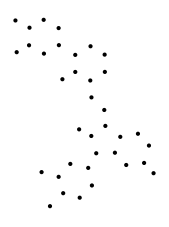

```mathematica
Graphics[mergedPoints]
```

Map the “other line finder” function over these points

```mathematica
mergedPointParents[#]&/@mergedPoints[[1;;2]]
```

{{Point[{72.0835,696.632}]},{Point[{76.4296,578.105}],Point[{77.0837,577.665}]}}

```mathematica
ReplacePart[#,{1,-1}->Mod[#,2]+1&@#[[1,-1]]]&/@(Position[cleanLines,mergedPointParents[#][[nTrace,1]]]&/@mergedPoints[[1;;2]])
```

{{{24,1,1}},{{16,1,2}}}

The index of the point index is one part of the edge (bond) list.

```mathematica
(Position[cleanLines,mergedPointParents[#][[nTrace,1]]]&/@mergedPoints)
```

{{{24,1,2}},{{16,1,1}},{{34,1,2}},{{34,1,1}},{{42,1,1}},{{27,1,1}},{{18,1,1}},{{51,1,1}},{{35,1,2}},{{35,1,1}},{{45,1,1}},{{43,1,1}},{{19,1,1}},{{44,1,1}},{{29,1,2}},{{21,1,2}},{{30,1,1}},{{54,1,1}},{{56,1,1}},{{39,1,1}},{{53,1,1}},{{64,1,2}},{{39,1,2},{40,1,2}},{{8,1,1}},{{56,1,2}},{{32,1,2}},{{5,1,1}},{{23,1,2}},{{2,1,2}},{{10,1,1}},{{61,1,1}},{{10,1,2}},{{13,1,2}},{{67,1,2}},{{13,1,1}},{{60,1,1}}}

What about the merged point that is traced to multiple lines?

```mathematica
mergedPointParents[[1]]
```

{Point[{72.0835,696.632}]}

```mathematica
mergedPoints[[1]]
```

Point[{7.27457,156.5}]

```mathematica
traceConnections[mergedPoints[[10]],cleanLines,mergedPoints,mergedPointParents,separatePointsChild]
```

{9,9,6}

Visualize this list as a graph

```mathematica
Transpose[{Range[Length[edgeListTargets]],edgeListTargets}]
```

{{1,{2,3}},{2,{4,1}},{3,{5,1}},{4,{6,2}},{5,{6,3}},{6,{5,4}}}

```mathematica
edgePairs=Thread/@Transpose[{Range[Length[edgeListTargets]],edgeListTargets}]
```

{{{1,4}},{{2,3},{2,3}},{{3,4},{3,7},{3,2},{3,2},{3,7}},{{4,3},{4,6},{4,1},{4,6}},{{5,11},{5,11}},{{6,10},{6,4},{6,4}},{{7,9},{7,3},{7,3}},{{8,12}},{{9,10},{9,16},{9,10},{9,7}},{{10,9},{10,9},{10,6}},{{11,12},{11,14},{11,5},{11,5},{11,12}},{{12,18},{12,11},{12,8},{12,18},{12,11}},{{13,15},{13,15}},{{14,19},{14,11}},{{15,20},{15,16},{15,13},{15,13},{15,16}},{{16,22},{16,15},{16,9},{16,15}},{{17,24},{17,24}},{{18,21},{18,21},{18,12},{18,12}},{{19,25},{19,21},{19,21},{19,19},{19,19},{19,21},{19,21},{19,19},{19,19},{19,14},{19,25}},{{20,23},{20,23},{20,28},{20,28},{20,23},{20,23},{20,15}},{{21,18},{21,19},{21,19},{21,21},{21,21},{21,19},{21,19},{21,21},{21,21},{21,18}},{{22,27},{22,27},{22,16}},{{23,20},{23,23},{23,23},{23,20},{23,23},{23,23},{23,26}},{{24,29},{24,29},{24,29},{24,25},{24,25},{24,24},{24,24},{24,25},{24,25},{24,24},{24,24},{24,17},{24,17}},{{25,19},{25,19},{25,24},{25,24},{25,25},{25,25},{25,24},{25,24},{25,25},{25,25},{25,30}},{{26,23},{26,29},{26,29}},{{27,22},{27,28},{27,22}},{{28,20},{28,27},{28,20}},{{29,24},{29,31},{29,26},{29,24},{29,31},{29,26},{29,24}},{{30,32},{30,32},{30,31},{30,31},{30,25},{30,31}},{{31,33},{31,29},{31,30},{31,30},{31,29},{31,30}},{{32,30},{32,34},{32,30},{32,34}},{{33,35},{33,35},{33,31},{33,35}},{{34,32},{34,36},{34,35},{34,32},{34,36}},{{35,33},{35,34},{35,33},{35,33}},{{36,34},{36,34}}}

```mathematica
Map[f@@#&,edgePairs,{2}]
```

{{f[1,2],f[1,3]},{f[2,4],f[2,1]},{f[3,5],f[3,1]},{f[4,6],f[4,2]},{f[5,6],f[5,3]},{f[6,5],f[6,4]}}

```mathematica
edgeList=Flatten@Map[UndirectedEdge@@#&,edgePairs,{2}];
```

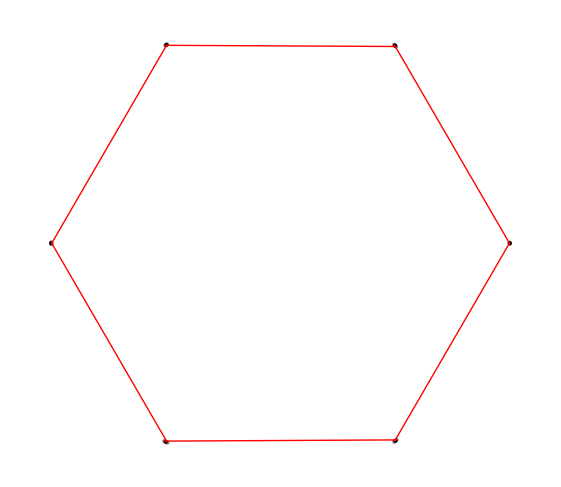

```mathematica
Graphics[{Gray,Point/@cleanPoints,Thick,Black,mergedPoints,Thin,Red,cleanLines}]
```

```mathematica
directedEdgeList=Flatten@Map[DirectedEdge@@#&,edgePairs,{2}]
```

{1->4,2->3,2->3,3->4,3->7,3->2,3->2,3->7,4->3,4->6,4->1,4->6,5->11,5->11,6->10,6->4,6->4,7->9,7->3,7->3,8->12,9->10,9->16,9->10,9->7,10->9,10->9,10->6,11->12,11->14,11->5,11->5,11->12,12->18,12->11,12->8,12->18,12->11,13->15,13->15,14->19,14->11,15->20,15->16,15->13,15->13,15->16,16->22,16->15,16->9,16->15,17->24,17->24,18->21,18->21,18->12,18->12,19->25,19->21,19->21,19->19,19->19,19->21,19->21,19->19,19->19,19->14,19->25,20->23,20->23,20->28,20->28,20->23,20->23,20->15,21->18,21->19,21->19,21->21,21->21,21->19,21->19,21->21,21->21,21->18,22->27,22->27,22->16,23->20,23->23,23->23,23->20,23->23,23->23,23->26,24->29,24->29,24->29,24->25,24->25,24->24,24->24,24->25,24->25,24->24,24->24,24->17,24->17,25->19,25->19,25->24,25->24,25->25,25->25,25->24,25->24,25->25,25->25,25->30,26->23,26->29,26->29,27->22,27->28,27->22,28->20,28->27,28->20,29->24,29->31,29->26,29->24,29->31,29->26,29->24,30->32,30->32,30->31,30->31,30->25,30->31,31->33,31->29,31->30,31->30,31->29,31->30,32->30,32->34,32->30,32->34,33->35,33->35,33->31,33->35,34->32,34->36,34->35,34->32,34->36,35->33,35->34,35->33,35->33,36->34,36->34}

```mathematica
{i,Graph[Range[Length[mergedPoints]],directedEdgeList]}
```

{-Graphics-,-Graphics-}

Should I remove duplicates?

Make the edge list from this in the following format: Bond[{1,2}]

## Build molecule

### Assuming carbon everywhere

```mathematica
edgeList
```

{1<->4,2<->3,2<->3,3<->4,3<->7,3<->2,3<->2,3<->7,4<->3,4<->6,4<->1,4<->6,5<->11,5<->11,6<->10,6<->4,6<->4,7<->9,7<->3,7<->3,8<->12,9<->10,9<->16,9<->10,9<->7,10<->9,10<->9,10<->6,11<->12,11<->14,11<->5,11<->5,11<->12,12<->18,12<->11,12<->8,12<->18,12<->11,13<->15,13<->15,14<->19,14<->11,15<->20,15<->16,15<->13,15<->13,15<->16,16<->22,16<->15,16<->9,16<->15,17<->24,17<->24,18<->21,18<->21,18<->12,18<->12,19<->25,19<->21,19<->21,19<->19,19<->19,19<->21,19<->21,19<->19,19<->19,19<->14,19<->25,20<->23,20<->23,20<->28,20<->28,20<->23,20<->23,20<->15,21<->18,21<->19,21<->19,21<->21,21<->21,21<->19,21<->19,21<->21,21<->21,21<->18,22<->27,22<->27,22<->16,23<->20,23<->23,23<->23,23<->20,23<->23,23<->23,23<->26,24<->29,24<->29,24<->29,24<->25,24<->25,24<->24,24<->24,24<->25,24<->25,24<->24,24<->24,24<->17,24<->17,25<->19,25<->19,25<->24,25<->24,25<->25,25<->25,25<->24,25<->24,25<->25,25<->25,25<->30,26<->23,26<->29,26<->29,27<->22,27<->28,27<->22,28<->20,28<->27,28<->20,29<->24,29<->31,29<->26,29<->24,29<->31,29<->26,29<->24,30<->32,30<->32,30<->31,30<->31,30<->25,30<->31,31<->33,31<->29,31<->30,31<->30,31<->29,31<->30,32<->30,32<->34,32<->30,32<->34,33<->35,33<->35,33<->31,33<->35,34<->32,34<->36,34<->35,34<->32,34<->36,35<->33,35<->34,35<->33,35<->33,36<->34,36<->34}

```mathematica
bondList=Apply[Bond@*List,edgeList,2]
```

{Bond[{1,4}],Bond[{2,3}],Bond[{2,3}],Bond[{3,4}],Bond[{3,7}],Bond[{3,2}],Bond[{3,2}],Bond[{3,7}],Bond[{4,3}],Bond[{4,6}],Bond[{4,1}],Bond[{4,6}],Bond[{5,11}],Bond[{5,11}],Bond[{6,10}],Bond[{6,4}],Bond[{6,4}],Bond[{7,9}],Bond[{7,3}],Bond[{7,3}],Bond[{8,12}],Bond[{9,10}],Bond[{9,16}],Bond[{9,10}],Bond[{9,7}],Bond[{10,9}],Bond[{10,9}],Bond[{10,6}],Bond[{11,12}],Bond[{11,14}],Bond[{11,5}],Bond[{11,5}],Bond[{11,12}],Bond[{12,18}],Bond[{12,11}],Bond[{12,8}],Bond[{12,18}],Bond[{12,11}],Bond[{13,15}],Bond[{13,15}],Bond[{14,19}],Bond[{14,11}],Bond[{15,20}],Bond[{15,16}],Bond[{15,13}],Bond[{15,13}],Bond[{15,16}],Bond[{16,22}],Bond[{16,15}],Bond[{16,9}],Bond[{16,15}],Bond[{17,24}],Bond[{17,24}],Bond[{18,21}],Bond[{18,21}],Bond[{18,12}],Bond[{18,12}],Bond[{19,25}],Bond[{19,21}],Bond[{19,21}],Bond[{19,19}],Bond[{19,19}],Bond[{19,21}],Bond[{19,21}],Bond[{19,19}],Bond[{19,19}],Bond[{19,14}],Bond[{19,25}],Bond[{20,23}],Bond[{20,23}],Bond[{20,28}],Bond[{20,28}],Bond[{20,23}],Bond[{20,23}],Bond[{20,15}],Bond[{21,18}],Bond[{21,19}],Bond[{21,19}],Bond[{21,21}],Bond[{21,21}],Bond[{21,19}],Bond[{21,19}],Bond[{21,21}],Bond[{21,21}],Bond[{21,18}],Bond[{22,27}],Bond[{22,27}],Bond[{22,16}],Bond[{23,20}],Bond[{23,23}],Bond[{23,23}],Bond[{23,20}],Bond[{23,23}],Bond[{23,23}],Bond[{23,26}],Bond[{24,29}],Bond[{24,29}],Bond[{24,29}],Bond[{24,25}],Bond[{24,25}],Bond[{24,24}],Bond[{24,24}],Bond[{24,25}],Bond[{24,25}],Bond[{24,24}],Bond[{24,24}],Bond[{24,17}],Bond[{24,17}],Bond[{25,19}],Bond[{25,19}],Bond[{25,24}],Bond[{25,24}],Bond[{25,25}],Bond[{25,25}],Bond[{25,24}],Bond[{25,24}],Bond[{25,25}],Bond[{25,25}],Bond[{25,30}],Bond[{26,23}],Bond[{26,29}],Bond[{26,29}],Bond[{27,22}],Bond[{27,28}],Bond[{27,22}],Bond[{28,20}],Bond[{28,27}],Bond[{28,20}],Bond[{29,24}],Bond[{29,31}],Bond[{29,26}],Bond[{29,24}],Bond[{29,31}],Bond[{29,26}],Bond[{29,24}],Bond[{30,32}],Bond[{30,32}],Bond[{30,31}],Bond[{30,31}],Bond[{30,25}],Bond[{30,31}],Bond[{31,33}],Bond[{31,29}],Bond[{31,30}],Bond[{31,30}],Bond[{31,29}],Bond[{31,30}],Bond[{32,30}],Bond[{32,34}],Bond[{32,30}],Bond[{32,34}],Bond[{33,35}],Bond[{33,35}],Bond[{33,31}],Bond[{33,35}],Bond[{34,32}],Bond[{34,36}],Bond[{34,35}],Bond[{34,32}],Bond[{34,36}],Bond[{35,33}],Bond[{35,34}],Bond[{35,33}],Bond[{35,33}],Bond[{36,34}],Bond[{36,34}]}

```mathematica
atomList=Table["C",Length[mergedPoints]]
```

{C,C,C,C,C,C}

```mathematica
molecule=Molecule[atomList,bondList]
```

Molecule::interr: An internal error occurred: Duplicate bond detected..

Molecule::interr: An internal error occurred: molecule has not been initialized.

General::stop: Further output of Molecule::interr will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

Molecule[{C,C,C,C,C,C},{Bond[{1,2}],Bond[{1,3}],Bond[{2,4}],Bond[{2,1}],Bond[{3,5}],Bond[{3,1}],Bond[{4,6}],Bond[{4,2}],Bond[{5,6}],Bond[{5,3}],Bond[{6,5}],Bond[{6,4}]}]

```mathematica
noDuplicateEdgePairs=DeleteDuplicates[Sort/@Flatten[edgePairs,1]]
```

{{1,4},{2,3},{3,4},{3,7},{4,6},{5,11},{6,10},{7,9},{8,12},{9,10},{9,16},{11,12},{11,14},{12,18},{13,15},{14,19},{15,20},{15,16},{16,22},{17,24},{18,21},{19,25},{19,21},{19,19},{20,23},{20,28},{21,21},{22,27},{23,23},{23,26},{24,29},{24,25},{24,24},{25,25},{25,30},{26,29},{27,28},{29,31},{30,32},{30,31},{31,33},{32,34},{33,35},{34,36},{34,35}}

```mathematica
noSelfBond=DeleteCases[noDuplicateEdgePairs,{ee_,ee_}]
```

{{1,4},{2,3},{3,4},{3,7},{4,6},{5,11},{6,10},{7,9},{8,12},{9,10},{9,16},{11,12},{11,14},{12,18},{13,15},{14,19},{15,20},{15,16},{16,22},{17,24},{18,21},{19,25},{19,21},{20,23},{20,28},{22,27},{23,26},{24,29},{24,25},{25,30},{26,29},{27,28},{29,31},{30,32},{30,31},{31,33},{32,34},{33,35},{34,36},{34,35}}

```mathematica
Position[noDuplicateEdgePairs,{x_,x_}]
```

{{24},{27},{29},{33},{34}}

```mathematica
noDuplicateEdgePairs[[24]]
```

{19,19}

```mathematica
bondList=Apply[Bond@*List,noSelfBond,2]
```

{Bond[{1,4}],Bond[{2,3}],Bond[{3,4}],Bond[{3,7}],Bond[{4,6}],Bond[{5,11}],Bond[{6,10}],Bond[{7,9}],Bond[{8,12}],Bond[{9,10}],Bond[{9,16}],Bond[{11,12}],Bond[{11,14}],Bond[{12,18}],Bond[{13,15}],Bond[{14,19}],Bond[{15,20}],Bond[{15,16}],Bond[{16,22}],Bond[{17,24}],Bond[{18,21}],Bond[{19,25}],Bond[{19,21}],Bond[{20,23}],Bond[{20,28}],Bond[{22,27}],Bond[{23,26}],Bond[{24,29}],Bond[{24,25}],Bond[{25,30}],Bond[{26,29}],Bond[{27,28}],Bond[{29,31}],Bond[{30,32}],Bond[{30,31}],Bond[{31,33}],Bond[{32,34}],Bond[{33,35}],Bond[{34,36}],Bond[{34,35}]}

```mathematica
molecule=Molecule[atomList,bondList]
```

Molecule[…]

### Tests

You can make a moleculue from an atom list and a bond list.

```mathematica
m2 = Molecule[{"N","C","Br","Cl","C"},{Bond[{1,2},"Single"],Bond[{2,3},"Single"],Bond[{2,4},"Single"],Bond[{2,5},"Single"]},StereochemistryElements->{<|"StereoType"->"Tetrahedral","ChiralCenter"->2,"Direction"->"Clockwise","FiducialAtom"->1,"Ligands"->{3,4,5}|>}]
```

Molecule[…]

```mathematica
m3=Molecule[{"N","C","Br","Cl","C"},{Bond[{1,2},"Single"],Bond[{2,3},"Single"],Bond[{2,4},"Single"],Bond[{2,5},"Single"]}]
```

Molecule[…]

## Make constants

```mathematica
?ChemicalRead`*
```

mergeThreshold